PhysicalConstants

```mathematica
<<PhysicalConstants`
Style[Names["PhysicalConstants`*"],10]
```

{AccelerationDueToGravity,AgeOfUniverse,AvogadroConstant,BohrRadius,BoltzmannConstant,ClassicalElectronRadius,CosmicBackgroundTemperature,DeuteronMagneticMoment,DeuteronMass,EarthMass,EarthRadius,ElectronCharge,ElectronComptonWavelength,ElectronGFactor,ElectronMagneticMoment,ElectronMass,FaradayConstant,FineStructureConstant,GalacticUnit,GravitationalConstant,HubbleConstant,IcePoint,MagneticFluxQuantum,MolarGasConstant,MolarVolume,MuonGFactor,MuonMagneticMoment,MuonMass,NeutronComptonWavelength,NeutronMagneticMoment,NeutronMass,PlanckConstant,PlanckConstantReduced,PlanckMass,ProtonComptonWavelength,ProtonMagneticMoment,ProtonMass,QuantizedHallConductance,RydbergConstant,SackurTetrodeConstant,SolarConstant,SolarLuminosity,SolarRadius,SolarSchwarzschildRadius,SpeedOfLight,SpeedOfSound,StefanConstant,ThomsonCrossSection,VacuumPermeability,VacuumPermittivity,WeakMixingAngle}

```mathematica
Units Package
```

13.4 Distance

```mathematica
<<PhysicalConstants`;G=GravitationalConstant;Subscript[m, E]=EarthMass;T=24Hour;r=((T^2 G Subscript[m, E])/(2π)^2)^(1/3);Subscript[r, E]=EarthRadius;Convert[r-Subscript[r, E],Meter]
```

3.58677×10^7 Meter

13.5 Kepler’s Laws

```mathematica
Graphics[Circle[{0,0},{4,2.5}],Axes -> True]
```

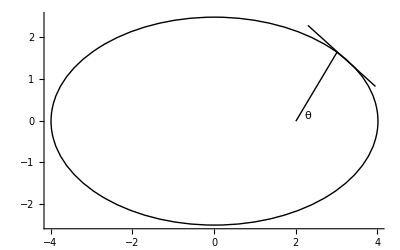

```mathematica
a=(G M)/r^2;
```

14 - 37

```mathematica
(0.1^2-0.05^2)/0.1^2 2.50
```

1.875

14-75

```mathematica
35.0/7860/8
```

0.000556616

14-83

```mathematica
0.075*(√2)/2*(0.3)^3*500*9.8
```

7.01627

14-93

```mathematica
Solve[4/3 π*(1.0*10^-3)^3*900*9.8-6π*1.5*10^-1*1.0*10^-3 x-4/3 π*(1.0*10^-3)^3*1.2*9.8==0,x]
```

{{x→0.0130492}}

```mathematica
Solve[4/3 π*(1.0*10^-3)^3*1000*9.8-6π*1.005*10^-1*10^-2*1.0*10^-3 x-4/3 π*(1.0*10^-3)^3*1.2*9.8==0,x]
```

{{x→2.16434}}

14-95

```mathematica
√(2*9.8*0.6)*0.2*10^-4
```

0.0000685857

```mathematica
√(2*9.8*0.6)*0.2*10^-4*8/π*(0.06*10^-1)/((0.4*10^-4/π)^2)*0.2/(800*9.8)
```

0.164899

```mathematica
√(2*9.8*0.6)*0.2*10^-4*8/π*(0.06*10^-1)/((1*10^-4/π)^2)*0.2/(800*9.8)
```

0.0263839

```mathematica
√(2*9.8*0.6)*0.2*10^-4*8/π*1/(1*10^-4/π)*1/4
```

1.37171

14-87

```mathematica
√((2000+1/2*1.20*120^2)/(1/2*1.20))
```

133.167

14-88

```mathematica
1/2*1.2*(200/3.6)^2-1/2*1.2*(200/3.6*30/350)^2
```

1838.25

```mathematica
1/2*(200/3.6)^2/9.8
```

157.47

12-60

```mathematica
D[1/2 m((G Subscript[M, E])/(r(1+x))),{x,2}]
D[1/2 m((G Subscript[M, E])/(r+Δr)),{Δr,2}]
```

(G m M_ⅇ)/(r (1+x)^3)

(G m M_ⅇ)/(r+Δr)^3

```mathematica
Series[1/2 m((G Subscript[M, E])/(r(1+x))),{x,0,10}]
```

(G m M_ⅇ)/(2 r)-((G m M_ⅇ) x)/(2 r)+(G m M_ⅇ x^2)/(2 r)-((G m M_ⅇ) x^3)/(2 r)+(G m M_ⅇ x^4)/(2 r)-((G m M_ⅇ) x^5)/(2 r)+(G m M_ⅇ x^6)/(2 r)-((G m M_ⅇ) x^7)/(2 r)+(G m M_ⅇ x^8)/(2 r)-((G m M_ⅇ) x^9)/(2 r)+(G m M_ⅇ x^10)/(2 r)+O[x]^11

```mathematica
(G m Subscript[M, ⅇ])/(2 r)+O[r]^11
```

```mathematica
Series[1/2 m((G Subscript[M, E])/(r+Δr)),{Δr,0,10}]
```

(G m M_ⅇ)/(2 r)-((G m M_ⅇ) Δr)/(2 r^2)+(G m M_ⅇ Δr^2)/(2 r^3)-((G m M_ⅇ) Δr^3)/(2 r^4)+(G m M_ⅇ Δr^4)/(2 r^5)-((G m M_ⅇ) Δr^5)/(2 r^6)+(G m M_ⅇ Δr^6)/(2 r^7)-((G m M_ⅇ) Δr^7)/(2 r^8)+(G m M_ⅇ Δr^8)/(2 r^9)-((G m M_ⅇ) Δr^9)/(2 r^10)+(G m M_ⅇ Δr^10)/(2 r^11)+O[Δr]^11

```mathematica
Series[r^p(1+x)^p,{x,0,5}]
```

r^p+p r^p x+1/2 (-1+p) p r^p x^2+1/6 (-2+p) (-1+p) p r^p x^3+1/24 (-3+p) (-2+p) (-1+p) p r^p x^4+1/120 (-4+p) (-3+p) (-2+p) (-1+p) p r^p x^5+O[x]^6

```mathematica
Series[(r+Δr)^p,{Δr,0,5}]
```

r^p+p r^(-1+p) Δr+1/2 (-1+p) p r^(-2+p) Δr^2+1/6 (-2+p) (-1+p) p r^(-3+p) Δr^3+1/24 (-3+p) (-2+p) (-1+p) p r^(-4+p) Δr^4+1/120 (-4+p) (-3+p) (-2+p) (-1+p) p r^(-5+p) Δr^5+O[Δr]^6

15-29

```mathematica
1/2*1.3*10^-3*1020*57*20*60
```

45349.2

15-40

```mathematica
(25*10^-2)/(62.1*2.4*10^-5)
```

167.74

15-47

```mathematica
(400*3480*6.0)/(2.42*10^6)
```

3.45124

15-38

```mathematica
Solve[70.0*3480*(37.0-T) ==0.355*4190(T-12.0),T]
```

{{T→36.8483}}

15-79

```mathematica
20*10^10(2.0-1.2)*10^-5*120
```

1.92×10^8

15-99

```mathematica
(0.120*2*0.95*(20-(-8)))/(6.8*10^-2)
```

93.8824

```mathematica
(0.120*(2*0.95-(0.5)^2)*(20-(-8)))/(6.8*10^-2)+(0.80*(0.5)^2*(20-(-8)))/(12.45*10^-2)
```

126.509

```mathematica
126.50933144342073/93.88235294117646
```

1.34753

15-103

```mathematica
(1/2(0.25)^2)/((1.6(0-(-10)))/(0.92*10^3*334*10^3))
```

600156.

```mathematica
(1/2(40)^2)/((1.6(0-(-10)))/(0.92*10^3*334*10^3))
```

1.5364×10^10

15-116

```mathematica
280+(54*1.5*(47-36))/3600+1400*1.5+1.5*1*5.67*10^-8((273+47)^4-(273+36)^4)
```

2496.69

```mathematica
1.5*1*5.67*10^-8((273+47)^4-(273+36)^4)
```

116.445

```mathematica
2496.69274124695/(2.42*10^6)*3600
```

3.71409

```mathematica
280+(54*0.45*(47-36))/3600+1400*0.45+0.45*1*5.67*10^-8((273+47)^4-(273+36)^4)
```

945.008

```mathematica
945.007822374085/(2.42*10^6)*3600
```

1.4058

sec15.5

```mathematica
(∫_0^(2π) Sin[x]^2 ⅆx)/(2π)
(∫_0^(2π) Cos[x]^2 ⅆx)/(2π)
```

1/2

1/2

15-84

```mathematica
(∫_0^(2π) Sin[x]^2 Cos[x]ⅆx)/(2π)
```

0

15-2

```mathematica
344/(20*10^3)//N
```

0.0172

15-47

```mathematica
√1.01 245//N
```

246.222

sec16.3

```mathematica
Log[10,6]//N
```

0.778151

```mathematica
Log[10,2]//N
```

0.30103

16-3

```mathematica
1.42*10^5*(2π*150)/344*0.02*10^-3
```

7.78092

16-21

```mathematica
Log[10,25]//N
```

1.39794

16-27

```mathematica
344/(4*17*10^-2)//N
```

505.882

```mathematica
(3*344)/(4*17*10^-2)//N
```

1517.65

16-28

```mathematica
344/(4*2.4*10^-2)//N
```

3583.33

16-31

```mathematica
344/(4*7*10^-2)//N
```

1228.57

16-39

```mathematica
344/(4*1.14)-344/(4*1.16)
```

1.30067

16-43

```mathematica
(344-15)/344 392//N
```

374.907

```mathematica
(344+15)/(344+35)392//N
```

371.314

16-49

```mathematica
200*10^6*√((2.99792458*10^8+20.1)/(2.99792458*10^8-20.1))√((2.99792458*10^8+20.1)/(2.99792458*10^8-20.1))
```

2.×10^8

```mathematica
2.0000002681855503*^8
```

```mathematica
200*10^6*√((3*10^8+20.1)/(3*10^8-20.1))√((3*10^8+20.1)/(3*10^8-20.1))
```

2.×10^8

```mathematica
2.0000002680000177*^8
```

16-66

```mathematica
344/(4*2.5*10^-2)
```

3440.

16-77

```mathematica
Solve[Subscript[f, r]==Subscript[f, b] (Subscript[v, s]+Subscript[v, i])/(Subscript[v, s]-Subscript[v, b])(Subscript[v, s]+Subscript[v, b])/(Subscript[v, s]-Subscript[v, i]),Subscript[v, i]]
```

{{v_i→(-f_b v_b v_s-f_r v_b v_s-f_b v_s^2+f_r v_s^2)/(f_b v_b-f_r v_b+f_b v_s+f_r v_s)}}

16-79

```mathematica
2*952*(0.018*10^14)/(4.568*10^14)*(360*60)/5*1/(2π)
```

5158.43

17.5 Heat

```mathematica
<<PhysicalConstants`;c=(4190Joule)/(Kilogram*Kelvin);m=4Kilogram;ΔT=100Kelvin;P=1500Watt;
Convert[(c m ΔT)/(P*(60Second)/Minute),Minute]//N
```

18.6222 Minute

```mathematica
<<PhysicalConstants`;c=(4190Joule)/(Kilogram*Kelvin);m=5Kilogram;ΔT=100Kelvin;P=1500Watt;
Convert[(c m ΔT)/P,Second]//N
```

1396.67 Second

18-12

```mathematica
(8.314*350)/(400*10^-6)
(8.314*350)/(400*10^-6-4.27*10^-5)-0.364/((400*10^-6)^2)
```

7.27475×10^6

5.86914×10^6

```mathematica
(8.314*350)/(4000*10^-6)
(8.314*350)/(4000*10^-6-4.27*10^-5)-0.364/((4000*10^-6)^2)
```

727475.

712575.

18-15

```mathematica
(100*1.013*10^5*3.10*10^-3)/(11*8.314)-273.15
```

70.2248

18-17

```mathematica
Solve[Exp[-(28.8*10^-3*9.8*y)/(8.314*273)]==0.9,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→847.29}}

18-19

```mathematica
Exp[-(28.8*10^-3*9.8*100)/(8.314*273)]
```

0.987642

18-20

```mathematica
Exp[-(28.8*10^-3*9.8*100*10^3)/(8.314*273)]
```

3.97692×10^-6

18-28

```mathematica
((22.4*10^-3)/(6.022*10^23))^(1/3)
```

3.33812×10^-9

18-37

```mathematica
3/2 1.381*10^-23*300
```

6.2145×10^-21

```mathematica
√((3*1.381*10^-23*300)/((32*10^-3)/(6.022*10^23)))
```

483.63

```mathematica
484*(32*10^-3)/(6.022*10^23)
```

2.5719×10^-23

```mathematica
(2*2.57*10^-23)/((2*0.10)/484)
```

1.24388×10^-19

18-63

```mathematica
Solve[4.20*10^5 0.50/(4-h)+10^3*9.80*h==1.0*10^5+10^3*9.80*1.0,h]
```

{{h→1.73661},{h→13.4675}}

18-69

```mathematica
(9.80*10^5)/(8.314*400)
```

294.684

13-39

```mathematica
12*13-2*6*7
```

72

18-76

```mathematica
√((3*8.314*5800)/(2*10^-3))
```

8504.81

18-89

```mathematica
1.81/4.25
```

0.425882

18-92

```mathematica
1.00*Exp[(28.8*10^-3*9.80)/(8.314*0.6/100)*Log[(288-0.6/100*8863)/288]]
```

0.315068

18-93

```mathematica
D[(n R T)/(V-n b)-(a n^2)/V^2,V]
D[(n R T)/(V-n b)-(a n^2)/V^2,V,V]
```

(2 a n^2)/V^3-(n R T)/(-b n+V)^2

-(6 a n^2)/V^4+(2 n R T)/(-b n+V)^3

```mathematica
Solve[(2 a n^2)/V^3-(n R T)/(-b n+V)^2==0,T]
```

{{T→(2 a n (b n-V)^2)/(R V^3)}}

```mathematica
(n R T)/(V-n b)-(a n^2)/V^2
```

```mathematica
(8.314*33.3)/(13.0*10^5*65.0*10^-6)
```

3.2764

19-13

```mathematica
(4*19+9*7)/510//N
```

0.272549

19-19

```mathematica
1.013*10^5*2*0.824
```

166942.

19-53

```mathematica
1.2*10^-2*791*2.51*10^3*30
(3*10^4*1.2*10^-3*30*1.2*10^-2)/0.02
```

714748.

648.

19-54

```mathematica
(2*10^-2)^3*8.9*10^3*390*70
1.01*10^5*5.1*10^-5*70*(2*10^-2)^3
```

1943.76

0.00288456

19-57

```mathematica
(273-15)((8.12/5.60)^(1/1.4))^0.4-273
```

13.8962

19-60

```mathematica
(1.45/1.01)^(1/1.4)
((1.45/1.01)^(1/1.4))^0.4
```

1.29472

1.10884

20-32

```mathematica
(2*452)/20.26
```

44.6199

```mathematica
(28*201)/77.34
```

72.7696

```mathematica
(32*213)/90.18
```

75.5822

```mathematica
(108*2336)/2466//N
```

102.307

20-35

```mathematica
2*8.314*Log[3]//N
```

18.2677

20-49

```mathematica
3.00*10^5*(0.8-0.5)*5/2
```

225000.

```mathematica
(1.00-3.00)*10^5*0.8*3/2
```

-240000.

20-53

```mathematica
1-1/10.6^0.40
```

0.611064

```mathematica
π((82.5*10^-3)/2)^2*86.4*10^-3*11.6/10.6
```

0.000505433

```mathematica
300*10.6^0.40
```

771.336

```mathematica
200/((8.50*10^4*5.10*10^-4)/(300*8.314)20.5)
```

561.33

```mathematica
771+561
```

1332

```mathematica
(771+561-300)/(771+561)//N
```

0.774775

20-55

```mathematica
4190*Log[273/373]//N
```

-1307.73

```mathematica
4190*(373-273)-Abs[4190*Log[273/373]]*273//N
```

61990.6

```mathematica
2*4190*(323-273)-Abs[2*4190*Log[273/323]]*273//N
```

34246.7

21-77

```mathematica
9.0*10^9((0.100*6.022*10^23*1.602*10^-19)^2)/((2.00*10^-2)^2)
```

2.09406×10^21

21-81

```mathematica
9.0*10^9((6.022*10^23*1.602*10^-19)^2)/((2*6.38*10^6)^2)
```

514455.

21-82

```mathematica
9.0*10^9((1.602*10^-19)^2)/((2*10^-15)^2)
```

57.7441

21-83

```mathematica
6.022*10^23*1.602*10^-19*10^-5*500
```

482.362

```mathematica
9.0*10^9(( 6.022*10^23*1.602*10^-19*10^-5*500)^2)/(5)^2
```

8.37624×10^13

22-23

```mathematica
-0.5/(4π(0.25)^2)+6.37
```

5.73338

```mathematica
-(0.5*10^-6)/(8.854*10^-12)
```

-56471.7

22-52

```mathematica
Solve[1/(2π)√((1/x^3*9.0*10^9*(1.602*10^-19)^2)/(9.109*10^-31))==4.57*10^14,x]
```

{{x→-1.56653×10^-10-2.71331×10^-10 ⅈ},{x→-1.56653×10^-10+2.71331×10^-10 ⅈ},{x→3.13306×10^-10}}

22-57

```mathematica
∫_0^R (3Q)/(π R^3)(1-x/R)4π x^2 ⅆx
```

Q

22-65

```mathematica
∫_0^R -Q/(π a^3)4π r^2 Exp[-(2r)/a]ⅆr
```

Q (-1+(ⅇ^(-(2 R)/a) (a^2+2 a R+2 R^2))/a^2)

22-66

```mathematica
∫_(R/2)^R 2α(1-r/R)4π r^2 ⅆr
```

11/24 π R^3 α

```mathematica
∫_(R/2)^R 2α(1-r/R)4π r^2 ⅆr+4/3 π (R/2)^3 α
```

5/8 π R^3 α

```mathematica
∫_(R/2)^t 2α(1-r/R)4π r^2 ⅆr+4/3 π (R/2)^3 α
```

-1/24 π R^3 α+8/3 π t^3 α-(2 π t^4 α)/R

23-3

```mathematica
3*9.0*10^9*((1.602*10^-19)^2)/(2*10^-15)
```

3.46465×10^-13

23-5

```mathematica
Solve[1/2*1.5*10^-3*v^2+9.0*10^9*(2.8*10^-6*7.8*10^-6)/0.4==1/2*1.5*10^-3*22^2+9.0*10^9*(2.8*10^-6*7.8*10^-6)/0.8,v]
```

{{v→-12.506},{v→12.506}}

```mathematica
Solve[9.0*10^9*(2.8*10^-6*7.8*10^-6)/r==1/2*1.5*10^-3*22^2+9.0*10^9*(2.8*10^-6*7.8*10^-6)/0.8,r]
```

{{r→0.322918}}

23-12

```mathematica
Solve[9.0*10^9*((1.602*10^-19)^2)/r==2*1/2*1.67*10^-27*(10^6)^2,r]
```

{{r→1.38309×10^-13}}

23-15

```mathematica
Solve[1/2*2*10^-4*v^2+(-5.0)*10^-6*800==1/2*2*10^-4*5^2+(-5.0)*10^-6*200,v]
```

{{v→-7.4162},{v→7.4162}}

23-21

```mathematica
9.0*10^9*(2.4*10^-9)/0.05+9.0*10^9*(-6.5*10^-9)/0.05
```

-738.

```mathematica
9.0*10^9*(2.4*10^-9)/0.08+9.0*10^9*(-6.5*10^-9)/0.06
```

-705.

```mathematica
-705.0000000000001*2.5*10^-9-(-738.*2.5*10^-9)
```

8.25×10^-8

23-33

```mathematica
Solve[(9.0*10^9*(24*10^-9)/(√(0.15^2+0.3^2))-9.0*10^9*(24*10^-9)/0.15)(-1.602*10^-19)==1/2*9.109*10^-31 v^2,v]
```

{{v→-1.67329×10^7},{v→1.67329×10^7}}

23-55

```mathematica
240/((13*10^-3)^(4/3))//N
```

78515.1

```mathematica
78515.14528301357*4/3
```

104687.

23-59

```mathematica
-9.0*10^9*((1.60*10^-19)^2)/(1/2*1.07*10^-10)*2
```

-8.61308×10^-18

```mathematica
Solve[-9.0*10^9*((1.60*10^-19)^2)/(1/2*1.07*10^-10)*2+1/2*9.11*10^-31*(1.5*10^6)^2==-9.0*10^9*((1.60*10^-19)^2)/(√(x^2+(1/2*1.07*10^-10)^2))*2,x]
```

{{x→-2.87293×10^-11},{x→2.87293×10^-11}}

22-83

```mathematica
∫_-R^R ∫_0^(√(R^2-x^2)) 1/(4π Subscript[ε, 0])Q/(√((x+2R)^2+y^2))Q/(4/3 π R^3)2π yⅆyⅆx
```

If[R∈Reals,(Q^2 Abs[R])/(8 π R^2 ε_0),Integrate[(3 Q^2 √(R (5 R+4 x)))/(8 π R^3 ε_0)-(3 Q^2 Abs[2 R+x])/(8 π R^3 ε_0),{x,-R,R},Assumptions→R∉Reals]]

```mathematica
∫_0^(√(R^2-x^2)) 1/(4π Subscript[ε, 0])Q/(√((x+2R)^2+y^2))Q/(4/3 π R^3)2π yⅆy
```

0

```mathematica
D[a/x+b/(c-x),x]
```

b/(c-x)^2-a/x^2

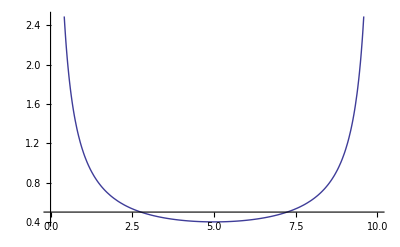

```mathematica
Plot[1/x+1/(10-x),{x,0,10}]
```

23-85

```mathematica
Solve[9.0*10^9*((1.60*10^-19)^2)/(2*1.2*10^-15)==2*1/2*1.67*10^-27*v^2,v]
```

{{v→-7.58189×10^6},{v→7.58189×10^6}}

```mathematica
Solve[9.0*10^9*((2*1.60*10^-19)^2)/(3.5*10^-15)==2*1/2*2.99*1.67*10^-27*v^2,v]
```

{{v→-7.26178×10^6},{v→7.26178×10^6}}

```mathematica
Solve[9.0*10^9*((1.60*10^-19)^2)/(2*1.2*10^-15)==2*3/2*1.381*10^-23*T,T]
```

{{T→2.31716×10^9}}

```mathematica
Solve[9.0*10^9*((2*1.60*10^-19)^2)/(3.5*10^-15)==2*3/2*1.381*10^-23*T,T]
```

{{T→6.35564×10^9}}

23-87

```mathematica
(1/2)^(1/3)//N
```

0.793701

```mathematica
Solve[9.0*10^9*((92/2*1.60*10^-19)^2)/(2*(1/2)^(1/3)*7.4*10^-15)== k ,k]
```

{{k→4.1503×10^-11}}

```mathematica
2*9.0*10^9*((92/2*1.60*10^-19)^2)/(2*(1/2)^(1/3)*7.4*10^-15)
```

8.30061×10^-11

```mathematica
10/(236*1.66*10^-27)
```

2.55258×10^25

```mathematica
10/(236*1.66*10^-27)*2*9.0*10^9*((92/2*1.60*10^-19)^2)/(2*(1/2)^(1/3)*7.4*10^-15)
```

2.1188×10^15

```mathematica
(4633/(236*1.66*10^-27)*2*9.0*10^9*((92/2*1.60*10^-19)^2)/(2*(1/2)^(1/3)*7.4*10^-15))
```

9.81639×10^17

```mathematica
(4633/(236*1.66*10^-27)*2*9.0*10^9*((92/2*1.60*10^-19)^2)/(2*(1/2)^(1/3)*7.4*10^-15))/(4.18*10^12)
```

234842.

23-89

```mathematica
Solve[{√(2*11.0*10^6*1.602*10^-19*2*1.67*10^-27)*1*10^-12==p r,11.0*10^6*1.602*10^-19-1/2 p^2/(2*1.67*10^-27)==9.0*10^9*(2*82*(1.60*10^-19)^2)/r},{p,r}]
```

{{p→-1.09666×10^-19,r→-9.89336×10^-13},{p→1.0734×10^-19,r→1.01078×10^-12}}

23-90

```mathematica
((L/2-x)+√((L/2-x)^2+R^2))/((-L/2-x)+√((L/2+x)^2+R^2))
```

```mathematica
(L+√((L/2-x)^2+R^2)-√((L/2+x)^2+R^2))/((-L/2-x)+√((L/2+x)^2+R^2))//FullSimplify
```

(4 L)/(-2 L+√(4 R^2+(L-2 x)^2)+√(4 R^2+(L+2 x)^2))

```mathematica
((L+√((L/2-x)^2+R^2)-√((L/2+x)^2+R^2))(-L+√((L/2-x)^2+R^2)+√((L/2+x)^2+R^2)))/(((-L/2-x)+√((L/2+x)^2+R^2))(-L+√((L/2-x)^2+R^2)+√((L/2+x)^2+R^2)))
```

```mathematica
(-2L x-L^2+2L √((L/2+x)^2+R^2))/(((-L/2-x)+√((L/2+x)^2+R^2))(-L+√((L/2-x)^2+R^2)+√((L/2+x)^2+R^2)))
```

```mathematica
(L/(√(x^2+R^2))-(L x)/(x^2+R^2))/(-(L/2)/(√(x^2+R^2))-x/(√(x^2+R^2))+1+1/2(L x)/(x^2+R^2))//FullSimplify
```

-(2 L)/(L-2 √(R^2+x^2))

```mathematica
(L/(√(x^2+R^2))(1-x/(√(x^2+R^2))))/((1-x/(√(x^2+R^2)))-1/2 L/(√(x^2+R^2))(1-x/(√(x^2+R^2))))
```

```mathematica
(L/(√(x^2+R^2)))/(1-1/2 L/(√(x^2+R^2)))//Simplify
```

-(2 L)/(L-2 √(R^2+x^2))

23-92

```mathematica
(6*10^-5*400+3*10^-5*1300)/(6*10^-5+3*10^-5)
```

```mathematica
1/2*6*10^-5*400^2+1/2*3*10^-5*1300^2-1/2*(6*10^-5+3*10^-5)((6*10^-5*400+3*10^-5*1300)/(6*10^-5+3*10^-5))^2-9.0*10^9*(2*10^-6*5*10^-6)/(9*10^-3)
```

-1.9

```mathematica
Solve[1/2*6*10^-5*400^2+1/2*3*10^-5*1300^2-9.0*10^9*(2*10^-6*5*10^-6)/(9*10^-3)==1/2*(6*10^-5+3*10^-5)((6*10^-5*400+3*10^-5*1300)/(6*10^-5+3*10^-5))^2-9.0*10^9*(2*10^-6*5*10^-6)/r,r]
```

{{r→0.0473684}}

24-15

```mathematica
28*2.4*10^-6//ScientificForm
```

6.72×10^-5

```mathematica
28*2.4*1/3
```

22.4

```mathematica
28*2.4*2/3
```

44.8

```mathematica
28*2.4/4
```

16.8

```mathematica
28*2.4*2/3/4
```

11.2

24-25

```mathematica
1/2*8.85*10^-12*(400/(5*10^-3))^2
```

0.02832

24-31

```mathematica
√(2*1*5.0*10^-6)
```

0.00316228

24-35

```mathematica
(2*3.2*10^-9)/4
```

1.6×10^-9

```mathematica
Exp[2π*8.85*10^-12*15/((2*3.2*10^-9)/4^2)]
```

8.04646

24-39

```mathematica
(3.20*10^5-2.50*10^5)*8.85*10^-12
```

6.195×10^-7

```mathematica
(3.20*10^5)/(2.50*10^5)
```

1.28

24-45

```mathematica
(2.32+1.85)/1.85
```

2.25405

## 24-47

```mathematica
1/2*12.5*10^-6*24^2
```

0.0036

```mathematica
1/2*3.75*12.5*10^-6*24^2
```

0.0135

24-62

```mathematica
(8.85*10^-12*π(10^3)^2)/(3*10^3)
```

9.2677×10^-9

```mathematica
20/((8.85*10^-12*π(10^3)^2)/(3*10^3))
```

2.15803×10^9

```mathematica
(20/((8.85*10^-12*π(10^3)^2)/(3*10^3)))/(3*10^3)
```

719344.

```mathematica
20/(π(10^3)^2*8.85*10^-12)//N
```

719344.

```mathematica
20^2/(2*(8.85*10^-12*π(10^3)^2)/(3*10^3))
```

2.15803×10^10

24-67

```mathematica
4π*8.85*10^-12*6380*10^3
```

0.000709535

24-73

```mathematica
Subscript[V, ac]=(Subscript[q, 1]-Subscript[q, z])/Subscript[c, y]
```

```mathematica
Subscript[V, bc]=(Subscript[q, 2]+Subscript[q, z])/Subscript[c, x]
```

```mathematica
Solve[(Subscript[q, 1]-Subscript[q, z])/Subscript[c, y]-(Subscript[q, 2]+Subscript[q, z])/Subscript[c, x]==Subscript[q, z]/Subscript[c, z],Subscript[q, z]]
```

{{q_z→(c_z (c_x q_1-c_y q_2))/(c_x c_y+c_x c_z+c_y c_z)}}

```mathematica
Coefficient[(Subscript[q, 1]-(Subscript[c, z] (Subscript[c, x] Subscript[q, 1]-Subscript[c, y] Subscript[q, 2]))/(Subscript[c, x] Subscript[c, y]+Subscript[c, x] Subscript[c, z]+Subscript[c, y] Subscript[c, z]))/Subscript[c, y],Subscript[q, 1]]//Simplify
```

(c_x+c_z)/(c_y c_z+c_x (c_y+c_z))

```mathematica
Coefficient[(Subscript[q, 1]-(Subscript[c, z] (Subscript[c, x] Subscript[q, 1]-Subscript[c, y] Subscript[q, 2]))/(Subscript[c, x] Subscript[c, y]+Subscript[c, x] Subscript[c, z]+Subscript[c, y] Subscript[c, z]))/Subscript[c, y],Subscript[q, 2]]//Simplify
```

c_z/(c_y c_z+c_x (c_y+c_z))

```mathematica
(Subscript[q, 1]-(Subscript[c, z] (Subscript[c, x] Subscript[q, 1]-Subscript[c, y] Subscript[q, 2]))/(Subscript[c, x] Subscript[c, y]+Subscript[c, x] Subscript[c, z]+Subscript[c, y] Subscript[c, z]))/Subscript[c, y]//Simplify
```

(c_x q_1+c_z (q_1+q_2))/(c_y c_z+c_x (c_y+c_z))

```mathematica
Collect[(Subscript[c, x] Subscript[q, 1]+Subscript[c, z] (Subscript[q, 1]+Subscript[q, 2]))/(Subscript[c, y] Subscript[c, z]+Subscript[c, x] (Subscript[c, y]+Subscript[c, z])),{Subscript[q, 1],Subscript[q, 2]}]
```

((c_x+c_z) q_1)/(c_y c_z+c_x (c_y+c_z))+(c_z q_2)/(c_y c_z+c_x (c_y+c_z))

```mathematica
Subscript[c, x]=6   
Subscript[c, y]=18  
Subscript[c, z]=27
Subscript[c, 1]=1/(Subscript[c, x]/(Subscript[c, y] Subscript[c, z]+Subscript[c, x] (Subscript[c, y]+Subscript[c, z])))
Subscript[c, 2]=1/(Subscript[c, y]/(Subscript[c, y] Subscript[c, z]+Subscript[c, x] (Subscript[c, y]+Subscript[c, z])))
Subscript[c, 3]=1/(Subscript[c, z]/(Subscript[c, y] Subscript[c, z]+Subscript[c, x] (Subscript[c, y]+Subscript[c, z])))
```

6

18

27

126

42

28

```mathematica
1/(1/42+1/21)
```

14

```mathematica
1/(1/72+1/126+1/28+1/72)
```

14

```mathematica
36*14
```

504

```mathematica
504/72
```

7

```mathematica
36-504/72-504/72-504/126
```

18

```mathematica
18*14
```

252

```mathematica
504/126+9
```

13

```mathematica
18*13
```

234

```mathematica
(18*14)/42
```

6

24-75

```mathematica
((Subscript[ϵ, 0] L/D((K-1)x+L))^2 V^2)/(2(Subscript[ϵ, 0] L/D((K-1)(x+Δx)+L)))-((Subscript[ϵ, 0] L/D((K-1)x+L))^2 V^2)/(2(Subscript[ϵ, 0] L/D((K-1)x+L)))//Simplify
```

-((-1+K) L V^2 (L+(-1+K) x) Δx ϵ_0)/(2 D (L+(-1+K) (x+Δx)))

24-77

```mathematica
2*8.85*10^-12*4.2*(0.12)^2/0.00045
```

2.37888×10^-9

25-17

```mathematica
1.72*10^-8*24/(π*(1/2*2.05*10^-3)^2)
```

0.125067

25-29

```mathematica
(5.60*10^-6)/120
```

4.66667×10^-8

25-37

```mathematica
0.11/1.65
```

0.0666667

25-40

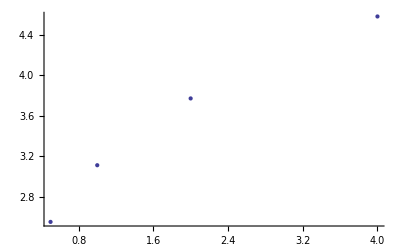

```mathematica
ListPlot[{{0.50,2.55},{1.00,3.11},{2.00,3.77},{4.00,4.58}},AxesOrigin->{0,0}]
```

25-49

```mathematica
Solve[12*60*3600==x*900*4.6*10^7,x]
```

{{x→0.0000626087}}

25-67

```mathematica
(0.00088+18*10^-5+0.00088*18*10^-5*40)
```

0.00106

25-73

```mathematica
Solve[3.2 x+3.8x+1.3 x^2==12.6,x]
```

{{x→-6.80823},{x→1.42362}}

25-77

```mathematica
1.72*10^-8*42/(π (0.326/2*10^-2)^2)(4200/120)^2
```

106.02

```mathematica
(1.72*10^-8*42/(π (0.326/2*10^-2)^2)(4200/120)^2-1.72*10^-8*42/(π (0.412/2*10^-2)^2)(4200/120)^2)*1/1000*12*365
```

173.629

```mathematica
(1.72*10^-8*42/(π (0.326/2*10^-2)^2)(4200/120)^2-1.72*10^-8*42/(π (0.412/2*10^-2)^2)(4200/120)^2)*0.11/1000*12*365
```

19.0992

25-79

```mathematica
(4/10)^2*10//N
```

1.6

```mathematica
(4/10)*12//N
(4/10)*8//N
```

4.8

3.2

25-81

```mathematica
(12+0.24*10)*10*5*3600
```

2.592×10^6

```mathematica
0.24*10^2*5*3600
```

432000.

```mathematica
12*10*5*3600-0.24*10^2*5*3600
```

1.728×10^6

26-27

```mathematica
24+(24/75+15/50)*20//N
```

36.4

26-29

```mathematica
40/175//N
```

0.228571

```mathematica
40/175*75//N
```

17.1429

26-31

```mathematica
0.5/19.5*25
```

0.641026

```mathematica
(500*10^-3)/(500*10^-6)-25
```

975

26-37

```mathematica
1.52/(2.5*10^-3)-65
```

543.

26-39

```mathematica
Solve[Exp[-4/(3.4*10^6*x)]==1/4,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→8.48644×10^-7}}

```mathematica
Solve[Exp[-4/x]==1/4,x]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2.88539},{x→0.034693+0.314483 ⅈ},{x→0.133941-0.607068 ⅈ},{x→0.133941+0.607068 ⅈ}}

26-41

```mathematica
Solve[Exp[-3/7 x/(80*15*10^-6)]==1/4.5,x]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{x->0.004211416710973567}}
10/80//N
```

{{x→0.00421142}}

0.125

```mathematica
Solve[Exp[-x/(80*35*10^-6)]==1/4.5,x]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.00421142}}

26-45

```mathematica
((3.5*10^-9)/(15*10^-12)+(3.5*10^-9)/(20*10^-12)+(3.5*10^-9)/(10*10^-12))*√0.2/25
```

13.5655

26-47

```mathematica
100/(90+(50*25)/(50+25))//N
```

0.9375

```mathematica
100/165//N
```

0.606061

26-49

```mathematica
1.50*10^-5*18(1-Exp[-(10*10^-3)/(980*1.50*10^-5)])
```

0.000133251

```mathematica
18(1-Exp[-(10*10^-3)/(980*1.50*10^-5)])
```

8.88338

```mathematica
1.50*10^-5*18(1-Exp[-(10*10^-3)/(980*1.50*10^-5)])*Exp[-(10*10^-3)/(980*1.50*10^-5)]
```

0.0000674887

26-53

```mathematica
120/(20(1+2.8*10^-3*(280-23)))
```

3.48918

26-55

```mathematica
(7.8*10^-8*20/(π((10*10^-2)/2)^2)*1.72*10^-8*20/(π(((20*10^-2)/2)^2-((10*10^-2)/2)^2)))/(7.8*10^-8*20/(π((10*10^-2)/2)^2)+1.72*10^-8*20/(π(((20*10^-2)/2)^2-((10*10^-2)/2)^2)))
```

0.0000136001

```mathematica
(7.8*10^-8*20/(π((10*10^-2)/2)^2)*1.72*10^-8*20/(π(((20*10^-2)/2)^2-((10*10^-2)/2)^2)))/(7.8*10^-8*20/(π((10*10^-2)/2)^2)+1.72*10^-8*20/(π(((20*10^-2)/2)^2-((10*10^-2)/2)^2)))*(π((20*10^-2)/2)^2)/20
```

2.13631×10^-8

26-59

```mathematica
1/(1/100+1/50+1/(1/(1/75+1/40)+1/(1/25+1/50)))//N
```

18.7302

```mathematica
1/(1/10+1/(7+1/(1/60+1/(20+1/(1/30+1/45)))))//N
```

7.51647

26-63

```mathematica
Solve[{14-2x-20+4y==0,-4y-5(x+y)-36==0},{x,y}]//N
```

{{x→-5.21053,y→-1.10526}}

26-65

```mathematica
12-4/9*4-10//N
```

0.222222

26-67

```mathematica
Solve[{70.6*10^-3*10+12+30*(70.6*10^-3-x-y)==0,-30*(70.6*10^-3-x-y)-24+10y==0},{x,y}]//N
```

{{x→-0.635267,y→1.1294}}

```mathematica
-1.1294*10+24
```

12.706

26-73

```mathematica
Solve[{6x-3y+3z==0,3(x-z)-3z-6(y+z)==0,6(y+z)+3y-36==0},{x,y,z}]//N
```

{{x→3.42857,y→5.14286,z→-1.71429}}

```mathematica
36/(3.4285714285714284+5.142857142857143)
```

4.2

26 - 75

```mathematica
Solve[{0.02*(48+y+z)==x*(10-0.02),0.02*(48+z)==(x+y)*(1-0.02),0.02*48==(x+y+z)*(0.1-0.02)},{x,y,z}]//N
```

{{x→0.12,y→1.08,z→10.8}}

26-77

```mathematica
1/(1/50+1/200)
1/(1/5000+1/200)
```

40

2500/13

```mathematica
400*40/140//N
```

114.286

```mathematica
400*(2500/13)/(100+2500/13)//N
```

263.158

```mathematica
400*200/(100+200)//N
```

266.667

26-85

```mathematica
Solve[7.00*10^-6 Exp[-x/(0.92*10^-6*670*10^3)]==1.6*10^-19,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→19.3608}}

26-89

```mathematica
Solve[{92-140x-210(x+y)+55==0,-55+210(x+y)+35y-57==0},{x,y}]//N
```

{{x→0.3,y→0.2}}

```mathematica
a={92/(140+1/(1/210+1/35)),92/(140+1/(1/210+1/35))35/(35+210),-92/(140+1/(1/210+1/35))210/(35+210)}
```

{46/85,46/595,-276/595}

```mathematica
b={-57/(35+1/(1/140+1/210))210/(140+210),57/(35+1/(1/140+1/210))140/(140+210),57/(35+1/(1/140+1/210))}
```

{-171/595,114/595,57/119}

```mathematica
c={55/(210+1/(1/140+1/35))35/(35+140),55/(210+1/(1/140+1/35)),55/(210+1/(1/140+1/35))140/(35+140)}
```

{11/238,55/238,22/119}

```mathematica
a+b+c//N
```

{0.3,0.5,0.2}

26-90

```mathematica
1000*10*10^-12
```

```mathematica
Solve[1*10^-6==(0.1*1000)/(1.1x)Exp[-(200*10^-6)/(1.1*10*10^-12 x)],x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→7.15076×10^6},{x→7.01537×10^7}}

```mathematica
D[-(200*10^-6)/(Log[(1.1*1*10^-6 t)/(0.1*1000)]*1.1*10*10^-12),t]/.t->1000000
```

0.893946

```mathematica
f[x_]:=-(200*10^-6)/(Log[(1.1*1*10^-6 x)/(0.1*1000)]*1.1*10*10^-12)
x=100
y=f[x]
While[Abs[x-y]≥1,x=y;y=f[x]]
x//N
```

100

1.32519×10^6

7.15076×10^6

26-93

```mathematica
n=1
While[(1/(1+((2(2+√3))/(1+√3))))^n>0.01,n++]
n
```

1

4

```mathematica
(1/(1+((2(2+√3))/(1+√3))))^4//N
```

0.00515478

```mathematica
Subscript[R, 1]=6.4*10^3
Subscript[R, 2]=8.0*10^8
Subscript[R, T]=Subscript[R, 1]+√(Subscript[R, 1]+2 Subscript[R, 1]*Subscript[R, 2])
β=2 Subscript[R, 1](Subscript[R, T]+Subscript[R, 2])/(Subscript[R, T]*Subscript[R, 2])
1/(1+β)
(1/(1+β))^((2*10^-3)/10^-6)
```

6400.

8.×10^8

3.2064×10^6

0.00400802

0.996008

0.000335459

```mathematica
Subscript[R, 1]=6.4*10^3
Subscript[R, 2]=3.3*10^12
Subscript[R, T]=Subscript[R, 1]+√(Subscript[R, 1]+2 Subscript[R, 1]*Subscript[R, 2])
β=2 Subscript[R, 1](Subscript[R, T]+Subscript[R, 2])/(Subscript[R, T]*Subscript[R, 2])
1/(1+β)
(1/(1+β))^((2*10^-3)/10^-6)
```

6400.

3.3×10^12

2.0553×10^8

0.0000622819

0.999938

0.882885

27-19

```mathematica
Solve[2*9.0*10^9*((1.60*10^-19)^2)/10^-15==2*1/2*3.34*10^-27*v^2,v]
```

{{v→-1.17458×10^7},{v→1.17458×10^7}}

```mathematica
Solve[3.34*10^-27*(1.2*10^7)/2.5==1.60*10^-19 B,B]
```

{{B→0.1002}}

27-27

```mathematica
1.60*10^-19*2.00*10^5*0.5
```

1.6×10^-14

```mathematica
1/2*1.31*10^-7*1.5*10^5+1/2*(2.00*10^4*1.60*10^-19)/(1.67*10^-27)*(1/2*1.31*10^-7)^2
```

0.0139354

27-31

```mathematica
(0.31*1.60*10^-19*0.54^2)/(1.12*10^5)
```

1.29137×10^-25

27-43

```mathematica
(2π *5.3*10^-11)/(2.2*10^6)
```

1.51368×10^-16

```mathematica
(1.60*10^-19)/((2π *5.3*10^-11)/(2.2*10^6))
```

0.00105703

```mathematica
(1.60*10^-19)/((2π *5.3*10^-11)/(2.2*10^6))*π *(5.3*10^-11)^2
```

9.328×10^-24

27-47

```mathematica
-2*1.45*0.835
```

2.4215

## 27-49

```mathematica
120/106//N
```

1.13208

```mathematica
4.82-120/106
```

3.68792

```mathematica
120-5.9(4.82-120/106)
```

98.2412

```mathematica
(120-5.9(4.82-120/106))(4.82-120/106)
```

362.306

27-51

```mathematica
120/(5.85*10^28*1.60*10^-19*11.8*0.23*10^-6)
```

0.00472384

```mathematica
0.95*120/(5.85*10^28*1.60*10^-19*11.8*0.23*10^-6)
```

0.00448765

```mathematica
0.95*120/(5.85*10^28*1.60*10^-19*11.8*0.23*10^-6)*11.8*10^-3
```

0.0000529543

27-59

```mathematica
Solve[x*0.75*1.55*(√3)/2==0.458*9.8,x]
```

{{x→4.45829}}

27-60

```mathematica
(5.0*10^-5*0.5^2)/2 √((1.60*10^-19)/(2*9.11*10^-31*750))
```

0.0676293

27-66

```mathematica
√(26/24)//N
```

1.04083

27-71

```mathematica
2.16/1.99*25
```

27.1357

27-75

```mathematica
Solve[0.15*10^-1*6*10^-2*9.8*8*10^-2*1/2+2*0.15*10^-1*8*10^-2*9.8*1/2*8*10^-2*1/2==8.2*6*10^-2*x*8*10^-2*(√3)/2,x]
```

{{x→0.0241501}}

27-79

```mathematica
50*2π*(1.56*10^-2)/2*0.95*0.22*(√3)/2
```

0.443528

27-83

```mathematica
Solve[x^2/(2*9.8)==0.35,x]
```

{{x→-2.61916},{x→2.61916}}

```mathematica
Solve[(0.35*2*9.8)/(2*(x*0.15*0.0065)/(5.4*10^-5))==0.025,x]
```

{{x→7.59877}}

28-15

```mathematica
(2*10^-7*20*10^3)/5//N
```

0.0008

28-20

```mathematica
(2*10^-7*800)/5.50//N
```

0.0000290909

28-21

```mathematica
2*(2*10^-7*4)/(√(0.05^2+0.2^2))0.2/(√(0.05^2+0.2^2))//N
```

7.52941×10^-6

28-23

```mathematica
2*2*(2*10^-7*100)/(√(0.1^2+0.1^2))0.1/(√(0.1^2+0.1^2))//N
```

0.0004

28-25

```mathematica
(2*10^-7*5*2*1.2)/0.4
```

6.×10^-6

28-27

```mathematica
(2*10^-7(100/120)^2)/(3.0*10^-3)
```

0.0000462963

28-33

```mathematica
(4Pi*10^-7*600*0.5*((4*10^-2)/2)^2)/(2(((4*10^-2)/2)^2)^(3/2))
```

0.00942478

```mathematica
(4Pi*10^-7*600*0.5*((4*10^-2)/2)^2)/(2((8*10^-2)^2+((4*10^-2)/2)^2)^(3/2))
```

0.000134461

28-35

```mathematica
(3.83*10^-4)/(4Pi*10^-7)
```

304.782

28-45

```mathematica
(4π*10^-7*600*0.65)/(2π*0.14*1/2)
```

0.00111429

28-48

```mathematica
Solve[(x*4π*10^-7*500*2.4)/(2π*0.25)==1.94,x]
```

{{x→2020.83}}

28-49

```mathematica
4π*10^-7*60*10^2*0.15
```

0.00113097

```mathematica
60*10^2*0.15*5199
```

4.6791×10^6

```mathematica
4π*10^-7*60*10^2*0.15*5200
```

5.88106

28-50

```mathematica
{273.15-258.15,273.15-173,273.15-73,273.15+27}
```

{15.,100.15,200.15,300.15}

```mathematica
{129,19.4,9.7,6.5}*{273.15-258.15,273.15-173,273.15-73,273.15+27}
```

{1935.,1942.91,1941.45,1950.98}

28-51

```mathematica
(4π*10^-7)/(4π)*(5*10^-6*6.5*10^4)/0.4^2+(4π*10^-7)/(4π)*(8*10^-6*9*10^4)/0.3^2
```

1.00313×10^-6

```mathematica
8*10^-6*9*10^4*(4π*10^-7)/(4π)*(5*10^-6*6.5*10^4*4/5)/0.5^2
```

7.488×10^-8

28-53

```mathematica
(1.6*10^-19*250*10^3*(4π*10^-7*25)/(2π*2*10^-2))/(9.1*10^-31)
```

1.0989×10^13

```mathematica
250*10^3*(4π*10^-7*25)/(2π*2*10^-2)//N
```

62.5

28-55

```mathematica
2(4π*10^-7*1.5*0.2^2)/(2((0.25/2)^2+0.2^2)^(3/2))
```

5.7472×10^-6

28-57

```mathematica
Solve[(4π*10^-7)/(4π)*(-7.20*10^-3*x)/0.25^2==6*10^-6,x]
```

{{x→-520.833}}

```mathematica
√(800^2-(-521)^2)//N
```

607.091

28-63

```mathematica
Solve[Tan[6Degree]*0.0125*9.8==(4π*10^-7*x^2)/(2π*2*0.04*Sin[6Degree]),x]
```

{{x→-23.202},{x→23.202}}

28-67

```mathematica
D[1/(((x+a/2)^2+a^2)^(3/2))+1/(((x-a/2)^2+a^2)^(3/2)),x]/.x->0
```

0

```mathematica
D[1/(((x+a/2)^2+a^2)^(3/2))+1/(((x-a/2)^2+a^2)^(3/2)),{x,2}]/.x->0
```

0

28-83

```mathematica
(6.5*10^4)/((7.8*10^3)/55.845*6.022*10^23)
```

7.72791×10^-22

28-84

```mathematica
(0.02^3*7.8*10^3*9.8)/1400*3.2
```

0.00139776

```mathematica
(0.02^3*7.8*10^3*9.8)/(1400*0.02^3*2.7*10^3*9.8)*3.2
```

0.00660317

29-9

```mathematica
(57*10^-2)/(2π)*12*10^-2*0.5
```

0.0054431

29-23

```mathematica
Solve[x*0.65*0.05==1.5,x]
```

{{x→46.1538}}

29-24

```mathematica
180*0.44704*0.5*10^-4*1.5
```

0.00603504

```mathematica
568*0.44704*0.5*10^-4*64.4
```

0.817618

29-39

```mathematica
2.0*10^-8*16/(2.1*(10^-3)^2)
```

0.152381

```mathematica
2.0*10^-8*4000/(2.1*(10^-3)^2)
```

38.0952

```mathematica
8.854*10^-12*2.0*10^-8*4000/(2.1*(10^-3)^2)
```

3.37295×10^-10

```mathematica
(4π*10^-7*(16+7.0832*^-16))/(2π*6*10^-2)
```

0.0000533333

29-43

```mathematica
(55*10^-3)/(4π*10^-7)//N
```

43767.6

29-47

```mathematica
Solve[Exp[-(2*0.1)/(π*4π*10^-7*0.5)t]==0.01,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.0000454512}}

29-75

```mathematica
0.1/2*0.035
0.1/2*0.035*√2
```

0.00175

0.00247487

```mathematica
0.1/2*0.035*4*0.2/1.90
```

0.000736842

```mathematica
0.1/2*0.035*1/2*0.2
```

0.000175

29-76

```mathematica
1/2*0.035*(0.1+0.2+0.1)*0.2
```

0.0014

30-15

```mathematica
(4π*10^-7*400*80)/0.25
```

0.16085

```mathematica
(((4π*10^-7*400*80)/0.25)^2)/(2(4π*10^-7))
```

10294.4

```mathematica
(((4π*10^-7*400*80)/0.25)^2)/(2(4π*10^-7))*(0.5*10^-4)*0.25
```

0.12868

```mathematica
Solve[(((4π*10^-7*400*80)/0.25)^2)/(2(4π*10^-7))*(0.5*10^-4)*0.25==1/2*x*80^2,x]
```

{{x→0.0000402124}}

30-20

```mathematica
Solve[6.3/15(1-ⅇ^(-15/x 2*10^-3))==0.21,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.0432809}}

30-25

```mathematica
60/240 ⅇ^(-240/0.16*4*10^-4)
```

0.137203

```mathematica
(60/240 ⅇ^(-240/0.16*4*10^-4))*240
```

32.9287

```mathematica
Solve[ⅇ^(-240/0.16*x)==1/2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.000462098}}

30-27

```mathematica
6*6.0/8(1-ⅇ^(-8/2.5 t))
```

4.5 (1-ⅇ^(-3.2 t))

```mathematica
8*(6.0/8(1-ⅇ^(-8/2.5 t)))^2
```

4.5 (1-ⅇ^(-3.2 t))^2

```mathematica
2.5*(6.0/8(1-ⅇ^(-8/2.5 t)))D[(6.0/8(1-ⅇ^(-8/2.5 t))),t]
```

4.5 ⅇ^(-3.2 t) (1-ⅇ^(-3.2 t))

30-31

```mathematica
√(1/(1.5*6*10^-5))
```

105.409

```mathematica
(2π)/(√(1/(1.5*6*10^-5)))
```

0.0596075

```mathematica
6*10^-5*12//N
```

0.00072

```mathematica
1/2*6*10^-5*12^2//N
```

0.00432

```mathematica
6*10^-5*12Cos[√(1/(1.5*6*10^-5))*0.023]
```

-0.000542637

```mathematica
-√(1/(1.5*6*10^-5))*(6*10^-5*12)Sin[√(1/(1.5*6*10^-5))*0.023]
```

-0.0498827

30-43

```mathematica
4π*10^-7*6750/(50*10^-2)*15*π*((0.12*10^-2)/2)^2
```

2.87798×10^-7

```mathematica
4π*10^-7*6750/(50*10^-2)*15*π*((0.12*10^-2)/2)^2*37.5
```

0.0000107924

30-59

```mathematica
Solve[0.4^2/(2*4π*10^-7)==1/2*3*10^-4*x^2,x]
```

{{x→-20601.3},{x→20601.3}}

30-60

```mathematica
1-ⅇ^-1//N
```

0.632121

30-61

```mathematica
ⅇ^-1//N
```

```mathematica
15/35*10//N
```

4.28571

```mathematica
50/35*10*3.0*10^-3
```

0.0428571

30-63

```mathematica
50/(50+(50*100)/(50+100))
```

3/5

30-75

```mathematica
Solve[0.6*Exp[-(x+120^2/40)/22*0.08]==0.15,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→21.2309}}

```mathematica
21.23094930796993*0.6
```

12.7386

```mathematica
12.738569584781958/(120^2/40)
```

0.0353849

30-77

```mathematica
(1/4*1.52*10^-3+1)*0.63
```

0.630239

31-14

```mathematica
√(200^2+(0.4*250-1/(6*10^-6*250))^2)
```

600.925

```mathematica
30/601//N
```

0.0499168

```mathematica
30/601*(0.4*250-1/(6*10^-6*250))
```

-28.2862

31-39

```mathematica
120^2/1600//N
```

9.

31-74

```mathematica
D[V/(√(R^2+(ω L-1/(ω c))^2))ω L,ω]//Simplify
```

(L V (2-2 c L ω^2+c^2 R^2 ω^2))/(√(R^2+(1/(c ω)-L ω)^2) (1-2 c L ω^2+c^2 ω^2 (R^2+L^2 ω^2)))

32-15

```mathematica
75/(4π(6/2*10^-2)^2)0.05
```

331.573

32-19

```mathematica
1/2*8.85*10^-12*3*10^8*0.09^2
```

0.0000107527

```mathematica
1/2*8.85*10^-12*3*10^8*0.09^2*4π(2.5*10^3)^2
```

844.519

32-30

```mathematica
(3*10^8)/(750*10^6)
```

2/5

32-35

```mathematica
(3*10^8)/(12.2*10^-2)(12.2/2*10^-2*5)/((12.2*10^-2)/2*5+5*10^-2)
```

2.11268×10^9

32-43

```mathematica
(3.9*10^26)/(4π*(6.96*10^8)^2)
```

6.40673×10^7

```mathematica
(3.9*10^26)/(4π*(6.96*10^8)^2*3*10^8)
```

0.213558

```mathematica
(3.9*10^26)/(4π*((6.96*10^8)/2)^2*3*10^8)
```

0.85423

32-45

```mathematica
1/2(8.85*10^-12)(3*10^8)1.25^2
```

0.00207422

```mathematica
Solve[4*10^-3*0.5^2*x==(1/2(8.85*10^-12)(3*10^8)1.25^2)/(3*10^8)(1.5*10^-2)^2*0.5,x]
```

{{x→7.77832×10^-13}}

32-51

```mathematica
Solve[1/2 200/(3*10^8*150)x^2==16,x]
```

{{x→-60000 √2},{x→60000 √2}}

```mathematica
(60000 √2)/3600//N
```

23.5702

32-53

```mathematica
Solve[(6.67*10^-11*5.97*10^24)/((x+6.38*10^6)^2)==((2π)/(12*3600))^2*(x+6.38*10^6),x]
```

{{x→-1.96806×10^7-2.30374×10^7 ⅈ},{x→-1.96806×10^7+2.30374×10^7 ⅈ},{x→2.02213×10^7}}

```mathematica
6.38*10^6+2.02*10^7
```

2.658×10^7

```mathematica
50/(2π*(2.02*10^7)^2)
```

1.95024×10^-14

```mathematica
(2.02*10^7)/(3*10^8)
```

0.0673333

```mathematica
50/(2π*(2.02*10^7)^2*3*10^8)
```

6.50079×10^-23

32-55

```mathematica
Solve[(6.67*10^-11*1.99*10^30)/1*3000*4/3 π*x^3==(3.9*10^26)/(4π*(3*10^8))π x^2,x]
```

{{x→0.},{x→0.},{x→1.94847×10^-7}}

32-56

```mathematica
((1.602*10^-19)^2((2*13.6*10^6*1.602*10^-19)/(0.0529*10^-9*1.67*10^-27))^2)/(6π*(8.85*10^-12)*(3*10^8)^3*13.6*10^6*1.602*10^-19)
```

6.36259×10^9

32-57

```mathematica
((1.602*10^-19)^2((2*6.0*10^6*1.602*10^-19)/(0.75*1.67*10^-27))^2)/(6π*(8.85*10^-12)*(3*10^8)^3*6.0*10^6*1.602*10^-19)
```

1.39648×10^-11

32-58

```mathematica
D[ⅇ^(-k x)Sin[k x-ω t],{x,2}]
```

-2 ⅇ^(-k x) k^2 Cos[k x-t ω]

```mathematica
D[{ⅇ^(-k x) k Cos[k x-t ω],ⅇ^(-k x) k Sin[k x-t ω]},{x,1}]
```

{-ⅇ^(-k x) k^2 Cos[k x-t ω]-ⅇ^(-k x) k^2 Sin[k x-t ω],ⅇ^(-k x) k^2 Cos[k x-t ω]-ⅇ^(-k x) k^2 Sin[k x-t ω]}

33-66

```mathematica
Table[Solve[3 Cos[θ ]^2==(n^2-1),θ],{n,{1.342,1.330}}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{{θ→-2.1138},{θ→-1.02779},{θ→1.02779},{θ→2.1138}},{{θ→-2.10164},{θ→-1.03995},{θ→1.03995},{θ→2.10164}}}

```mathematica
{1.0277939729667103/π*180,1.0399529852947011/π*180}
```

{58.8883,59.5849}

```mathematica
180-(π+2θ-4ArcSin[Sin[θ]/n])/π*180/.{θ->1.0277939729667103,n->1.342}
```

40.7872

```mathematica
180-(π+2θ-4ArcSin[Sin[θ]/n])/π*180/.{θ->1.0399529852947011,n->1.330}
```

42.5164

33-67

```mathematica
Table[Solve[8 Cos[θ ]^2==(n^2-1),θ],{n,{1.342,1.330}}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{{θ→-1.89275},{θ→-1.24884},{θ→1.24884},{θ→1.89275}},{{θ→-1.88601},{θ→-1.25558},{θ→1.25558},{θ→1.88601}}}

```mathematica
(2π+2θ-6ArcSin[Sin[θ]/n])/π*180-180/.{θ->1.2488449928094487,n->1.342}
```

53.2221

```mathematica
(2π+2θ-6ArcSin[Sin[θ]/n])/π*180-180/.{θ->1.2555820890009997,n->1.330}
```

50.1012

34-7

```mathematica
Solve[1/(5.58*10^10)+1/Subscript[s, 1]==1/1.75,Subscript[s, 1]]
```

{{s_1→1.75}}

```mathematica
1.75/(5.58*10^10)*6794*10^3
```

0.000213073

34-15

```mathematica
Solve[1.309/(3.5*10^-2)+1/Subscript[s, 1]==0,Subscript[s, 1]]
```

{{s_1→-0.026738}}

34-17

```mathematica
Solve[1.33/(14*10^-2)+1/Subscript[s, 1]==(1-1.33)/(-14*10^-2),Subscript[s, 1]]
```

{{s_1→-0.14}}

```mathematica
-(1.33*Subscript[s, 1])/(14*10^-2)/.{Subscript[s, 1]->-0.13999999999999999}
```

1.33

```mathematica
Solve[0+1.33/Subscript[s, 1]==(1.33-1)/(14*10^-2),Subscript[s, 1]]
```

{{s_1→0.564242}}

34-23

```mathematica
Solve[1/(22.5*10^-2)+1/Subscript[s, 1]==(1.7-1)(-1)1/(-13*10^-2),Subscript[s, 1]]
```

{{s_1→1.06364}}

```mathematica
-Subscript[s, 1]/(22.5*10^-2)*3.75*10^-3/.{{Subscript[s, 1]->1.0636363636363644}}
```

{-0.0177273}

34-27

```mathematica
Solve[-(-12*10^-2)/s==(3.4*10^-2)/(8*10^-3),s]
```

{{s→0.0282353}}

34-35

```mathematica
Solve[1/(20.4*10^-2)+1/s==1/(200*10^-3),s]
```

{{s→10.2}}

34-39

```mathematica
Solve[(1/(1/f-1/600))/600 240==36*10^-3,f]//N
```

{{f→0.0899865}}

```mathematica
Solve[(1/(1/f-1/40))/40 9.6==36*10^-3,f]//N
```

{{f→0.14944}}

34-40

```mathematica
Solve[1/(-8*10^-2)+1/Subscript[s, 1]==1/(-12*10^-2),Subscript[s, 1]]//N
```

{{s_1→0.24}}

```mathematica
Solve[1/(-4*10^-2)+1/Subscript[s, 1]==1/(-12*10^-2),Subscript[s, 1]]//N
```

{{s_1→0.06}}

34-43

```mathematica
Solve[1/(45*10^-2)+1/Subscript[s, 1]==1/(50*10^-3),Subscript[s, 1]]//N
```

{{s_1→0.05625}}

34-45

```mathematica
Solve[1/0.25+1/Subscript[s, 1]==2.75,Subscript[s, 1]]//N
Solve[1/Subscript[s, 1]==-1.30,Subscript[s, 1]]//N
```

{{s_1→-0.8}}

{{s_1→-0.769231}}

34-47

```mathematica
1/0.25+1/-0.60
```

2.33333

```mathematica
1/-0.60
```

-1.66667

34-49

```mathematica
Solve[1/-0.25+1/s==1/(8*10^-2),s]//N
```

{{s→0.0606061}}

34-57

```mathematica
-(95*10^-2)/(15*10^-2)//N
```

-6.33333

```mathematica
(1/(1/0.95-1/3000))/3000 60
```

0.019006

```mathematica
((1/(1/0.95-1/3000))/3000 60)/0.15
```

0.126707

34-75

```mathematica
Solve[1/2+1/Subscript[s, 1]==1/0.75,Subscript[s, 1]]//N
```

{{s_1→1.2}}

```mathematica
Solve[1/2.001+1/Subscript[s, 1]==1/0.75,Subscript[s, 1]]//N
```

{{s_1→1.19964}}

```mathematica
Subscript[s, 1]/2/.{{Subscript[s, 1]->1.2}}//N
```

{0.6}

34-77

```mathematica
(20*10^-2)/1.5*18*10^-2
```

0.024

```mathematica
(20*10^-2)/1.5
```

0.133333

34-78

```mathematica
Solve[1/(23*10^-2)+1.6/Subscript[s, 1]==(1.6-1)/(6*10^-2),Subscript[s, 1]]
```

{{s_1→0.283077}}

```mathematica
Solve[1.6/(0.40-0.283)+1/Subscript[s, 1]==(1-1.6)/(-12*10^-2),Subscript[s, 1]]
```

{{s_1→-0.115271}}

38-85

```mathematica
Solve[1.35/(25*10^-3)==(1.35-1)/r,r]
```

{{r→0.00648148}}

```mathematica
Solve[1/(25*10^-2)+1.35/Subscript[s, 1]==(1.35-1)/0.0065,Subscript[s, 1]]
```

{{s_1→0.0270833}}

```mathematica
Solve[1.35/Subscript[s, 1]==(1.35-1)/0.005,Subscript[s, 1]]
```

{{s_1→0.0192857}}

```mathematica
Solve[x/(25*10^-3)==(x-1)/0.0088,x]
```

{{x→1.54321}}

```mathematica
Solve[1.54/(25*10^-3)==(1.54-1)/r,r]
```

{{r→0.00876623}}

```mathematica
Solve[1.54/Subscript[s, 1]==(1.54-1)/0.005,Subscript[s, 1]]
```

{{s_1→0.0142593}}

34-93

```mathematica
Solve[{1/(0.6-x)+1/Subscript[s, 1]==1/(-0.36/2),1/(0.6-Subscript[s, 1])+1/x==1/(0.36/2)},{x,Subscript[s, 1]}]
```

{{x→0.24,s_1→-0.12},{x→0.72,s_1→0.36}}

```mathematica
Solve[{1/Subscript[s, 1]+1/x==1/(0.36/2),1/(0.6-x)+1/(0.6-Subscript[s, 1])==1/(-0.36/2)},{x,Subscript[s, 1]}]
```

{{x→0.24,s_1→0.72},{x→0.72,s_1→0.24}}

```mathematica
Solve[{1/Subscript[s, 1]+1/x==1/(0.36/2),1/(0.6-x)+1/(0.6+Subscript[s, 1])==1/(-0.36/2)},{x,Subscript[s, 1]}]
```

{{x→0.144358,s_1→-0.729028},{x→0.748142,s_1→0.237028}}

34-103

```mathematica
Solve[{1/s+1/Subscript[s, 1]==1/(35*10^-3),Subscript[s, 1]/s==(36*10^-3*1/4)/12},{s,Subscript[s, 1]}]//N
```

{{s→46.7017,s_1→0.0350263}}

34-115

```mathematica
sol=Table[Solve[1/s+1/a==1/0.20,a],{s,{0.45+0.08*(√2)/2,0.45,0.45-0.08*(√2)/2}}]
```

{{{a→0.330477}},{{a→0.36}},{{a→0.406792}}}

```mathematica
a/.sol
```

{{0.330477},{0.36},{0.406792}}

```mathematica
im=(a/.sol)[[All,1]]
ob={0.45+0.08*(√2)/2,0.45,0.45-0.08*(√2)/2}
obh={0.15-0.08*(√2)/2,0.15,0.15+0.08*(√2)/2}
```

{0.330477,0.36,0.406792}

{0.506569,0.45,0.393431}

{0.0934315,0.15,0.206569}

```mathematica
im/ob
imh=im/ob obh
```

{0.652383,0.8,1.03396}

{0.0609531,0.12,0.213583}

```mathematica
√((im[[3]]-im[[1]])^2+(imh[[3]]-imh[[1]])^2)
```

0.170646

34-116

```mathematica
ArcCos[1/1.02]/Degree
```

11.3649

34-119

```mathematica
Solve[1.40/(2.6*10^-2)==(1.40-1)/r,r]
```

{{r→0.00742857}}

```mathematica
Solve[1.33/x+1.40/(2.6*10^-2)==(1.40-1.33)/0.74,x]
```

{{x→-0.0247435}}

35.3

```mathematica
Degree//N
```

0.0174533

```mathematica
(θ/.Solve[2π Sin[θ]==3/4 π,θ])/Degree//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{22.0243}

35-9

```mathematica
75*10^-2*(500*10^-9)/(0.45*10^-3)
```

0.000833333

35-17

```mathematica
1/((585*10^-9)/(0.0116*10^-3))
```

19.8291

```mathematica
ArcSin[19((585*10^-9)/(0.0116*10^-3))]/Degree
```

73.3734

35-21

```mathematica
(2π 0.34*10^-3)/(500*10^-9)Sin[23Degree]
```

1669.42

35-23

```mathematica
1/2*(660*10^-9)/(0.26*10^-3)
```

0.00126923

```mathematica
1/2*(660*10^-9)/(0.26*10^-3)*0.7
```

0.000888462

35-25

```mathematica
1/4*((3*10^8)/(12.5*10^6))/56
```

0.107143

```mathematica
1/3*((3*10^8)/(12.5*10^6))/56*0.5*10^3
```

71.4286

35-27

```mathematica
1/4(650*10^-9)/1.42
```

1.14437×10^-7

35-33

```mathematica
(2*290)/(1/2)1.33//N
```

1542.8

```mathematica
(2*290)/(3/2)1.33//N
```

514.267

35-35

```mathematica
1/4*790/1.8//N
```

109.722

35-37

```mathematica
1800*(633*10^-9)/2//N
```

0.0005697

35-39

```mathematica
2*√((1/2(1+1/2)*580*10^-9+95.2*10^-2)^2-(95.2*10^-2)^2)
```

0.00182015

35-56

```mathematica
(2*74)/(1/2)1.80//N
```

532.8

35-61

```mathematica
2((3*10^-2(1+5*10^-6*5))/((589*10^-9)/(1.48+2.5*10^-5*5))-(3*10^-2)/((589*10^-9)/1.48)-(3*10^-2*5*10^-6*5)/(589*10^-9))
```

13.9562

36-1

```mathematica
(1.35*10^-3*0.75*10^-3)/2
```

5.0625×10^-7

36-3

```mathematica
1/((585*10^-9)/(0.0666*10^-3))
```

113.846

36-5

```mathematica
ArcSin[800/4500]//N
```

0.178728

36-9

```mathematica
ArcSin[(344/1250)/1]/Degree//N
```

15.9739

36-11

```mathematica
(620*10^-9)/(36.5*10^-2/√((40*10^-2)^2+(36.5*10^-2)^2))
```

9.19813×10^-7

36-15

```mathematica
(Sin[π/2]/(π/2))^2*6.00*10^-6
```

2.43171×10^-6

36-17

```mathematica
(2π)/56*0.105*10^-3 Sin[3.25Degree]
```

6.67896×10^-7

```mathematica
(Sin[56/2]/(56/2))^2//N
```

0.0000936096

36-27

```mathematica
90*10^-2*(500*10^-9)/(1*10^-2)//N
```

0.000045

36-33

```mathematica
ArcSin[(632.8*10^-9)/(1.60*10^-6)]/Degree//N
```

23.2972

36-36

```mathematica
(656.27*10^-9)/(656.45*10^-9-656.27*10^-9)*1/2
```

1822.97

36-37

```mathematica
5*10^3*3.5
```

17500.

```mathematica
Solve[(587.8002*10^-9)/x==2*17500,x]
```

{{x→1.67943×10^-11}}

```mathematica
Solve[(587.8002*10^-9-x)/x==2*17500,x]
```

{{x→1.67938×10^-11}}

```mathematica
587.8002*10^-9+1.6794291428571432*^-11
```

5.87817×10^-7

```mathematica
5.878169942914287*^-7
```

```mathematica
N[5878002*10^-4,20]
```

587.8002

```mathematica
587.8002*10^-9-1.6793811605382707*^-11
```

5.87783×10^-7

```mathematica
5.877834061883947*^-7
```

36-39

```mathematica
(0.085*10^-9)/Sin[21.5Degree]
```

2.31923×10^-10

36-41

```mathematica
1.22(550*10^-9)/(0.3/(60*60)Degree)
```

0.461346

36-47

```mathematica
1.22(500*10^-9)/(250*10^3)5.93*10^8*10^3
```

1.44692

36-49

```mathematica
1.22(400*10^-9)/2.4 3.84*10^8
```

78.08

```mathematica
1.22 0.75/305 3.84*10^8
```

1.152×10^6

36-51

```mathematica
1.22(550*10^-9)/10*4.28*9.461*10^15
```

2.71709×10^9

36-53

```mathematica
FindRoot[Sin[π 2Sin[θ]]/(π 2 Sin[θ])==(√2)/2,{θ,0.1}]
```

{θ→0.223325}

```mathematica
0.22332496467797563/Degree
```

12.7956

```mathematica
FindRoot[Sin[π 5Sin[θ]]/(π 5 Sin[θ])==(√2)/2,{θ,0.1}]
```

{θ→0.0887056}

```mathematica
Table[FindRoot[Sin[π k Sin[θ Degree]]/(π k Sin[θ Degree])==(√2)/2,{θ,0.01}],{k,{ 2 ,5,10}}]
```

{{θ→12.7956},{θ→5.08246},{θ→2.53873}}

```mathematica
(θ/.{{θ->12.795577935956189},{θ->5.082455411548211},{θ->2.5387269644188146}})*2
```

{25.5912,10.1649,5.07745}

```mathematica
Table[FindRoot[Sin[θ Degree]==1/k,{θ,0.01}],{k,{ 2 ,5,10}}]
```

{{θ→30.},{θ→11.537},{θ→5.73917}}

```mathematica
(θ/.{{θ->29.999999999999996},{θ->11.536959032815489},{θ->5.739170477266787}})*2
```

{60.,23.0739,11.4783}

36-55

```mathematica
Sin[38.2 Degree]/Sin[17.4 Degree]
```

2.06797

36-58

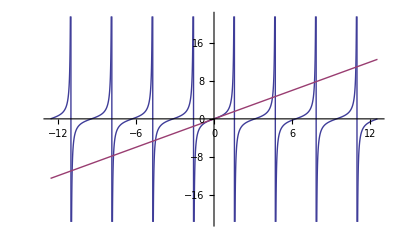

```mathematica
Plot[{Tan [γ],γ},{γ,-4Pi,4Pi}]
```

36-60

```mathematica
Sin[23.41 Degree]*(1*10^-2)/5758
```

6.90011×10^-7

```mathematica
Solve[(3*10^8)/(Sin[23.41 Degree]*(1*10^-2)/5758)√((3*10^8-v)/(3*10^8+v))==(3*10^8)/(656.3*10^-9),v]
```

{{v→-1.50141×10^7}}

```mathematica
v/(3*10^8)/.{{v->-1.5014102754211655*^7}}
```

{-0.050047}

36-68

```mathematica
1.22((3*10^8)/(1665*10^6))/(77000*10^3)*7.2*10^8*9.461*10^15
```

1.94467×10^16

36-69

```mathematica
Solve[(√2)/2==x ((3*10^8)/(8800*10^6))/(2π (28*10^-2)/14),x]//N
```

{{x→2.60649}}

36-72

```mathematica
1.22(10*10^-6)/1*4.28*9.461*10^15
```

4.94016×10^11

```mathematica
1.22(10*10^-6)/(6000*10^3)*59*9.461*10^15
```

1.135×10^6

37-3

```mathematica
(√3)/2*3*10^8//N
```

2.59808×10^8

37-7

```mathematica
365*24-√(1-((4.8*10^6)/(3*10^8))^2)*365*24
```

1.12135

37-9

```mathematica
74/(√(1-(0.6)^2))
```

92.5

37-11

```mathematica
2.2*10^-6*3*10^8*0.999
```

659.34

```mathematica
(2.2*10^-6)/(√(1-(0.999)^2))
```

0.0000492058

```mathematica
(2.2*10^-6)/(√(1-(0.999)^2))*3*10^8
```

14761.7

```mathematica
√(1-(0.999)^2)*10000
```

447.102

37-15

```mathematica
Table[(x+0.6c)/(1+(0.6c*x)/c^2),{x,{0.4c,0.9c,0.99c}}]
```

{0.806452 c,0.974026 c,0.997491 c}

```mathematica
(0.8c-0.6c)/(1-(0.6c*0.8c)/c^2)
```

0.384615 c

37-23

```mathematica
Solve[0.92c==(0.36c-x)/(1-(x*0.36c)/c^2),x]
```

{{x→-0.837321 c}}

37-25

```mathematica
((675/575)^2-1)/((675/575)^2+1)//N
```

0.158983

37-37

```mathematica
Solve[m(3*10^8)^2==1.0*10^19,m]
```

{{m→111.111}}

37-45

```mathematica
Solve[(1/(√(1-x^2))-1)==3/2 1/2 x^2,x]//N
```

{{x→0.},{x→-0.651899},{x→0.651899}}

37-46

```mathematica
1/(2.0136*2)(2.0136*2-4.0015)*(3*10^8)^2
```

5.74344×10^14

```mathematica
(1*10^19)/(5.74344*10^14)
```

17411.2

37-49

```mathematica
Solve[(1.2*10^3*√(1-x^2))/(2.6*10^-8)==x*3*10^8,x]
```

{{x→0.999979}}

```mathematica
1-x/.Solve[(1.2*10^3*√(1-x^2))/(2.6*10^-8)==x*3*10^8,x]
```

{0.0000211243}

```mathematica
0.00002112433062517738
```

```mathematica
139.6/(√(1-x^2))/.Solve[(1.2*10^3*√(1-x^2))/(2.6*10^-8)==x*3*10^8,x]
```

{21477.4}

37-51

```mathematica
Solve[√(1-x^2)==1/1.4,x]
```

{{x→-0.699854},{x→0.699854}}

37-55

```mathematica
Solve[(1/(√(1-(1-x)^2))-1)*1.67*10^-27*(3*10^8)^2==7*10^12*1.602*10^-19,x]
```

{{x→8.97946×10^-9},{x→2.}}

```mathematica
1/(√(1-(1-x)^2))/.Solve[(1/(√(1-(1-x)^2))-1)*1.67*10^-27*(3*10^8)^2==7*10^12*1.602*10^-19,x]
```

{7462.08,7462.08}

37-57

```mathematica
((1/(√(1-(1/1.52)^2))-1)*9.11*10^-31*(3*10^8)^2)/(1.602*10^-19)
```

167781.

37-59

```mathematica
(1/(√(1-(1/2)^2))-1)*1.67*10^-27*(3*10^8)^2
```

2.32515×10^-11

```mathematica
(1/(√(1-(4/5)^2))-1)*1.67*10^-27*(3*10^8)^2
```

1.002×10^-10

```mathematica
1/2*1.67*10^-27*(1/2*3*10^8)^2
```

1.87875×10^-11

```mathematica
1/2*1.67*10^-27*(4/5*3*10^8)^2
```

4.8096×10^-11

```mathematica
1/2*1.67*10^-27*(3*10^8)^2
```

7.515×10^-11

37-65

```mathematica
(√(5^2-(2.5)^2))/(3*10^8)
```

1.44338×10^-8

37-69

```mathematica
Grid[Table[{v,(500*9.461*10^15)/(v*365*24*3600),(500*9.461*10^15*√(1-(v/(3*10^8))^2))/(v*365*24*3600),(1/√(1-(v/(3*10^8))^2)-1)*1000*(3*10^8)^2,((1/√(1-(v/(3*10^8))^2)-1)*1000*(3*10^8)^2)/10^19},{v,{0.5*3*10^8,0.99*3*10^8,0.9999*3*10^8}}],Frame->All]//N
```

1.5×10^8 | 1000.02 | 866.044 | 1.3923×10^19 | 1.3923
2.97×10^8 | 505.061 | 71.2476 | 5.47993×10^20 | 54.7993
2.9997×10^8 | 500.061 | 7.07175 | 6.27412×10^21 | 627.412

```mathematica
Table[{v,(500*9.461*10^15)/v,(500*9.461*10^15*√(1-(v/(3*10^8))^2))/v,(1/√(1-(v/(3*10^8))^2)-1)*1000*(3*10^8)^2,((1/√(1-(v/(3*10^8))^2)-1)*1000*(3*10^8)^2)/10^19},{v,{0.5*3*10^8,0.99*3*10^8,0.9999*3*10^8}}]
```

{{1.5×10^8,3.15367×10^10,2.73116×10^10,1.3923×10^19,1.3923},{2.97×10^8,1.59276×10^10,2.24687×10^9,5.47993×10^20,54.7993},{2.9997×10^8,1.57699×10^10,2.23015×10^8,6.27412×10^21,627.412}}

37-72

```mathematica
1-1/1.33^2
```

0.434677

37-74

```mathematica
g=9.8;c=3*10^8;x=5*365*24*3600;(4(Tanh[(x g)/c]*c)/(g √(1-(Tanh[(x g)/c])^2)))/(365*24*3600)
```

335.045

37-75

```mathematica
(4.567710-4.568110)/4.568110*3*10^8
(4.568910-4.568110)/4.568110*3*10^8
((4.567710-4.568110)/4.568110*3*10^8+(4.568910-4.568110)/4.568110*3*10^8)/2
```

-26269.1

52538.1

13134.5

```mathematica
v=52.5*10^3-13.1*10^3
R=(52.5*10^3-13.1*10^3)/((2π)/(11*24*3600))
m=(v^2*4 R)/(6.67*10^-11)
```

39400.

5.95968×10^9

5.54817×10^29

37-77

```mathematica
Solve[(1/(√(1-(u/(3*10^8))^2))-1)938.3==493.7,u]
```

{{u→-2.26627×10^8},{u→2.26627×10^8}}

```mathematica
(2.266*10^8)/(3*10^8)
```

0.755333

```mathematica
(2u)/(1+(u/(3*10^8))^2)/.{u->2.266×10^8}
```

2.88565×10^8

```mathematica
2.8856529253140277*^8
```

```mathematica
(1/(√(1-(x/(3*10^8))^2))-1)*938.3/.x->2.886*10^8
```

2498.07

```mathematica
((1/(√(1-((2.886*10^8)/(3*10^8))^2))-1)*938.3)/(493.7*2)
```

2.52995

```mathematica
(2*(1/(√(1-((2.266*10^8)/(3*10^8))^2))-1)*938.3)/(493.7*2)
```

0.999543

38-1

```mathematica
5*1.60*10^-19
```

8.×10^-19

```mathematica
1.60*10^-19*7/(1.83*10^15)
```

6.12022×10^-34

```mathematica
1.60*10^-19*7/(1.83*10^15)*1.25
```

7.65027×10^-34

38-7

```mathematica
√((2*(4.136*10^-15*(3*10^8)/(235*10^-9)-5.1)*1.60*10^-19)/(9.11*10^-31))
```

251450.

38-15

```mathematica
1.097*10^7(1/2^2-1/5^2)*2.998*10^8
```

6.90649×10^14

```mathematica
1/(1.097*10^7(1/2^2-1/5^2))
```

4.34084×10^-7

```mathematica
1.097*10^7(1/2^2-1/5^2)*2.998*10^8*6.626*10^-34
```

4.57624×10^-19

38-17

```mathematica
-6.52+4.136*10^-15*(3*10^8)/(860*10^-9)
```

-5.07721

38-19

```mathematica
-17.5+4.136*10^-15*(3*10^8)/(94.54*10^-9)
```

-4.3754

38-21

```mathematica
9.0*10^9*(2*82*1.60*10^-19)/(6.50*10^-14)
```

3.63323×10^6

```mathematica
9.0*10^9*(2*82*(1.60*10^-19)^2)/(6.50*10^-14)
```

5.81317×10^-13

38-23

```mathematica
-13.60/-1.51
```

9.00662

```mathematica
3*(6.626*10^-34)/(2π)
```

3.16368×10^-34

38-25

```mathematica
13.60*16
```

217.6

```mathematica
(122*10^-19)/16//N
```

7.625×10^-19

38-27

```mathematica
5.29*10^-11*4
```

2.116×10^-10

```mathematica
(2.19*10^6)/2
```

1.095×10^6

```mathematica
(2π*5.29*10^-11*4)/((2.19*10^6)/2)
```

1.21418×10^-15

```mathematica
10^-8/((2π*5.29*10^-11*4)/((2.19*10^6)/2))
```

8.23604×10^6

38-29

```mathematica
7.5*10^-3/(6.626*10^-34*(3*10^8)/(10.6*10^-6))
```

3.9994×10^17

38-31

```mathematica
ⅇ^(-((20.66-18.70)*1.60*10^-19)/(1.38*10^-23*300))
```

1.26683×10^-33

```mathematica
ⅇ^(-((20.66-18.70)*1.60*10^-19)/(1.38*10^-23*1200))
```

5.96595×10^-9

38-33

```mathematica
(4.136*10^-15*3*10^8)/(4*10^3)
```

3.102×10^-10

38-35

```mathematica
(4.136*10^-15*3*10^8)/(25*10^3)
```

4.9632×10^-11

38-37

```mathematica
0.0665*10^-9+2*2.426*10^-12
```

7.1352×10^-11

38-39

```mathematica
2.426*10^-12*(1-Cos[35Degree])
```

4.38737×10^-13

```mathematica
2.426*10^-12*(1-Cos[35Degree])+0.0425*10^-9
```

4.29387×10^-11

```mathematica
(4.136*10^-15*3*10^8)/(0.0425*10^-9)-(4.136*10^-15*3*10^8)/(0.04294*10^-9)
```

299.16

38-43

```mathematica
Solve[30*10^-2*π*0.4*10^-3*0.26*5.67*10^-8*x^4==100,x]
```

{{x→-2059.58},{x→0.-2059.58 ⅈ},{x→0.+2059.58 ⅈ},{x→2059.58}}

```mathematica
Solve[x*2.06*10^3==2.9*10^-3,x]
```

{{x→1.40777×10^-6}}

38-45

```mathematica
Solve[x*2.728==2.9*10^-3,x]
```

{{x→0.00106305}}

```mathematica
(3*10^8)/(2450*10^6)//N
```

0.122449

38-49

```mathematica
D[(2π h c^2)/(λ^5(Exp[(h c)/(λ k T)]-1)),λ]//Simplify
```

(2 c^2 h π (c ⅇ^((c h)/(k T λ)) h-5 (-1+ⅇ^((c h)/(k T λ))) k T λ))/((-1+ⅇ^((c h)/(k T λ)))^2 k T λ^7)

```mathematica
c ⅇ^((c h)/(k T λ)) h-5 (-1+ⅇ^((c h)/(k T λ))) k T λ
```

38-48

```mathematica
Solve[x*24000==2.9*10^-3,x]
```

{{x→1.20833×10^-7}}

```mathematica
64.2*10^6*4π*(6.96*10^8)^2
```

3.90808×10^26

38-50

```mathematica
Solve[x*30000==2.9*10^-3,x]
```

{{x→9.66667×10^-8}}

38-51

```mathematica
(1*10^5)/(6.022*10^23)1/(1.602*10^-19)
```

1.03657

```mathematica
4.136*10^-15*100*10^6
```

4.136×10^-7

```mathematica
(4.136*10^-15*3*10^8)/(700*10^-9)
```

1.77257

38-57

```mathematica
2*10^-6*10^-3*4190*(100-33)+2*10^-6*10^-3*2.256*10^6
```

0.00507346

```mathematica
(5.1*10^-3)/(450*10^-6)
```

11.3333

38-59

```mathematica
(1836.2*207)/(1836.2+207)
```

186.028

```mathematica
(1836.2*207)/(1836.2+207)*9.109*10^-31
```

1.69453×10^-28

```mathematica
-186*13.60
```

-2529.6

```mathematica
(-186*13.60)/4-(-186*13.60)/1
```

1897.2

```mathematica
(4.136*10^-15*3*10^8)/((-186*13.60)/4-(-186*13.60)/1)
```

6.54016×10^-10

38-62

```mathematica
Solve[20*(2π*8060*10^3)/(2*3600)*8060*10^3==n*(6.626*10^-34)/(2π),n]
```

{{n→1.07517×10^46}}

38-65

```mathematica
(4.136*10^-15*3*10^8)/(85.5*10^-9)
```

14.5123

```mathematica
14.51 -13.60
```

0.91

38-67

```mathematica
(5.67*10^-8*3000^4*4π*(6.96*10^8*600)^2)/((6.626*10^-34*3*10^8)/((2.9*10^-3)/3000))
```

4.89444×10^49

```mathematica
(5.67*10^-8*3000^4*4π*(6.96*10^8*600)^2)/(5.67*10^-8*5800^4*4π*(6.96*10^8)^2)
```

25767.7

38-69

```mathematica
Solve[x*(4.136*10^-15*3*10^8)/((-13.6/16)-(-13.6))==2.9*10^-3,x]
```

{{x→29799.3}}

38-73

```mathematica
(500*10^-9-(4.136*10^-15*3*10^8)/10^6)/10^26
```

4.99999×10^-33

```mathematica
Solve[2.426*10^-12((x Degree)^2/2)==5*10^-33,x]
```

{{x→-3.67855×10^-9},{x→3.67855×10^-9}}

```mathematica
(10^6*365*24.0*3600*3*10^8)/10^26
```

0.000094608

38-75

```mathematica
(6.626*10^-34*3*10^8)/(0.11*10^-9)-(6.626*10^-34*3*10^8)/(0.1132*10^-9)
```

5.10838×10^-17

38-81

```mathematica
Solve[(p *c-Subscript[p, 1]* c +En)^2==(m c^2)^2+((√(En^2-(m c^2)^2))/c-p-Subscript[p, 1])^2*c^2,Subscript[p, 1]]
```

{{p_1→(-En p-√(En^2-c^4 m^2) p)/(-En+√(En^2-c^4 m^2)-2 c p)}}

```mathematica
Solve[h/Subscript[λ, 1]==(-En p-√(En^2-c^4 m^2) p)/(-En+√(En^2-c^4 m^2)-2 c p),Subscript[λ, 1]]
```

{{λ_1→(En h-h √(En^2-c^4 m^2)+2 c h p)/(En p+√(En^2-c^4 m^2) p)}}

```mathematica
Solve[(h/λ *c-h/Subscript[λ, 1]* c +𝔼)^2==(m c^2)^2+((√(𝔼^2-(m c^2)^2))/c-h/λ-h/Subscript[λ, 1])^2*c^2,Subscript[λ, 1]]
```

{{λ_1→(2 c h+𝔼 λ-√(-c^4 m^2+𝔼^2) λ)/(𝔼+√(-c^4 m^2+𝔼^2))}}

```mathematica
(p *c-Subscript[p, 1]* c +En)^2==(m c^2)^2+((√(En^2-(m c^2)^2))/c-p-Subscript[p, 1])^2*c^2
```

```mathematica
(p *c-Subscript[p, 1]* c +En)^2//Expand
```

En^2+2 c En p+c^2 p^2-2 c En p_1-2 c^2 p p_1+c^2 p_1^2

```mathematica
(m c^2)^2+((√(En^2-(m c^2)^2))/c-p-Subscript[p, 1])^2*c^2//Expand
```

En^2-2 c √(En^2-c^4 m^2) p+c^2 p^2-2 c √(En^2-c^4 m^2) p_1+2 c^2 p p_1+c^2 p_1^2

```mathematica
λ=10.6*10^-6;𝔼=10*10^9*1.60*10^-19;h=6.626*10^-34;c=3*10^8;m=9.11*10^-31;
(2 c h+𝔼 λ-√(-c^4 m^2+𝔼^2) λ)/(𝔼+√(-c^4 m^2+𝔼^2))
```

7.08293×10^-15

40-1

```mathematica
h=6.626*10^-34;ℏ=h/(2π);p=4.50*10^-24;k=p/ℏ;m=9.109*10^-31;ω=p^2/(2m*ℏ);
```

```mathematica
k
ω
```

4.26718×10^10

1.05403×10^17

40-2

```mathematica
(Subscript[k, 1]-Subscript[k, 2])x-(Subscript[ω, 1]-Subscript[ω, 2])t=(Subscript[k, 1]-Subscript[k, 2])(x-v*t)
```

```mathematica
A(ⅇ^(ⅈ(k x-ω t))-ⅇ^(ⅈ(2k x-4ω t)))A(ⅇ^(-ⅈ(k x-ω t))-ⅇ^(-ⅈ(2k x-4ω t)))=
A^2(2-ⅇ^(ⅈ(k x-ω t)-ⅈ(2k x-4ω t))-ⅇ^(-ⅈ(k x-ω t)+ⅈ(2k x-4ω t)))=
A^2(2-ⅇ^(-ⅈ(k x-3ω t))-ⅇ^(ⅈ(k x-3ω t)))=
A^2(2-2Cos[k x-3ω t))
```

```mathematica
ⅈ(k x-ω t)-ⅈ(2k x-4ω t)//Simplify
```

-ⅈ (k x-3 t ω)

```mathematica
k x=π    
Δx = (2π)/k
k x -3ω (2π)/ω=k x -6π =π
((7π)/k-π/k)/((2π)/ω)=(3ω)/k
```

40-3

```mathematica
A^2(2+2Cos[2k x-8ω t))
```

```mathematica
2k x-8ω (2π)/ω=2k x-16π=0
```

```mathematica
x=(8π)/k
```

```mathematica
((8π)/k)/((2π)/ω)=(4ω)/k
```

40-4

```mathematica
Subscript[v, av]=(Subscript[ω, 2]-Subscript[ω, 1])/(Subscript[k, 2]-Subscript[k, 1])=((ℏ Subscript[k, 2]^2)/(2m)-(ℏ Subscript[k, 1]^2)/(2m))/(Subscript[k, 2]-Subscript[k, 1])
```

40-5

```mathematica
A^2 Sin[k x]^2=A^2((1-Cos[2k x])/2)
```

```mathematica
2k x=π
2k x=0
```

40-6

```mathematica
ψ[x,t]=A ⅇ^(ⅈ k x)ⅇ^(ⅈ (E t)/ℏ);
(δ ψ[x,t])/(δ t)=A ⅇ^(ⅈ k x) ⅇ^(ⅈ (E t)/ℏ)(ⅈ E/ℏ)
```

40-8

40-25

```mathematica
-ℏ/(2m)(d^2 ψ[x])/(d t)^2+U ψ[x]=E ψ[x]
```

```mathematica
<<PhysicalConstants`
Style[Names["PhysicalConstants`*"],10]
```

{AccelerationDueToGravity,AgeOfUniverse,AvogadroConstant,BohrRadius,BoltzmannConstant,ClassicalElectronRadius,CosmicBackgroundTemperature,DeuteronMagneticMoment,DeuteronMass,EarthMass,EarthRadius,ElectronCharge,ElectronComptonWavelength,ElectronGFactor,ElectronMagneticMoment,ElectronMass,FaradayConstant,FineStructureConstant,GalacticUnit,GravitationalConstant,HubbleConstant,IcePoint,MagneticFluxQuantum,MolarGasConstant,MolarVolume,MuonGFactor,MuonMagneticMoment,MuonMass,NeutronComptonWavelength,NeutronMagneticMoment,NeutronMass,PlanckConstant,PlanckConstantReduced,PlanckMass,ProtonComptonWavelength,ProtonMagneticMoment,ProtonMass,QuantizedHallConductance,RydbergConstant,SackurTetrodeConstant,SolarConstant,SolarLuminosity,SolarRadius,SolarSchwarzschildRadius,SpeedOfLight,SpeedOfSound,StefanConstant,ThomsonCrossSection,VacuumPermeability,VacuumPermittivity,WeakMixingAngle}

```mathematica
h=PlanckConstant;ℏ=h/(2π);e=ElectronCharge;Subscript[m, e]=ElectronMass;Subscript[m, p]=ProtonMass;Subscript[m, n]=NeutronMass;Subscript[ϵ, 0]=VacuumPermittivity//N
```

(8.85419×10^-12 Ampere Second)/(Meter Volt)

40-32

```mathematica
h=PlanckConstant;ℏ=h/(2π);m=6.64*10^-27 Kilogram;L=2.0Femto Meter;
Subscript[U, 0]=30*10^6 ElectronVolt;
En=Subscript[U, 0]-1*10^6 ElectronVolt;
κ=(√(2m(Subscript[U, 0]-En)))/ℏ;G=16 En/Subscript[U, 0](1-En/Subscript[U, 0]);T=G ⅇ^(-2κ L)
Convert[T,1]
```

116/225 ⅇ^(-(4.37102×10^24 Femto √(ElectronVolt Kilogram) Meter)/(Joule Second))

0.0896262

40-38

```mathematica
-ℏ^2/(2m)D[ψ,{x,2}]+1/2 k1 x^2 ψ==En ψ
```

```mathematica
ψ=C Exp[-√(m k1)*x^2/(2ℏ)];D[ψ,{x,2}](-ℏ^2/(2m))//Simplify
```

(C ⅇ^(-(√(k1 m) x^2)/(2 ℏ)) (-k1 m x^2+√(k1 m) ℏ))/(2 m)

```mathematica
(√(k1 m) ℏ)/(2 m)=1/2 ω ℏ=En
```

40-39

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=0.25Kilogram;k1=(100Newton)/Meter; ω=√(k1/m);ΔE=ω ℏ
Convert[ΔE,ElectronVolt]
```

2.10914×10^-33 Joule √(Newton/(Kilogram Meter)) Second

1.31642×10^-14 ElectronVolt

40-40

```mathematica
<<PhysicalConstants`;h=PlanckConstant;c=SpeedOfLight;λ=8.65*10^-6 Meter; En=1/2(h c)/λ
Convert[En,ElectronVolt]
```

1.14823×10^-20 Joule

0.0716671 ElectronVolt

40-44

```mathematica
C Exp[-√(m k1)*((n+1/2)ℏ ω 2)/(2ℏ k1)]=C Exp[-√(m k1)*(n+1/2) ω/k1  ]
```

40-48

```mathematica
Solve[Exp[-α^2 k^2]==1/2,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→-(√Log[2])/α},{k→(√Log[2])/α}}

```mathematica
∫_0^∞ Exp[-α^2 k^2]Cos[k x]ⅆk
```

If[x∈Reals&&Re[α^2]>0,(ⅇ^(-x^2/(4 α^2)) √π)/(2 √(α^2)),Integrate[ⅇ^(-k^2 α^2) Cos[k x],{k,0,∞},Assumptions→x∉Reals||Re[α^2]≤0]]

```mathematica
Solve[ⅇ^(-x^2/(4 α^2))==1/2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2 α √Log[2]},{x→2 α √Log[2]}}

```mathematica
2 α √Log[2](h (√Log[2])/α)/(2π)
```

(h Log[2])/π

40-52

```mathematica
En=(n^2 π^2 ℏ^2)/(2m L^2)
```

```mathematica
(2n+1)/n^2
```

```mathematica
D[(2n+1)/n^2,n]
```

2/n^2-(2 (1+2 n))/n^3

```mathematica
2/n^2-(2 (1+2 n))/n^3==0
n-(1+2 n)==0
```

```mathematica
-1-n
```

```mathematica
En=-1/Subscript[ϵ, 0]^2(m ⅇ^4)/(8 n^2 h^4)
```

```mathematica
((-1/(n+1)^2)-(-1/(n)^2))/(-1/n^2)//Simplify
```

(-1-2 n)/(1+n)^2

40-55

```mathematica
Table[∫_((1L)/4)^((3L)/4) 2/L Sin[(n π x)/L]^2 ⅆx,{n,1,2}]//N
```

{0.81831,0.5}

40-59

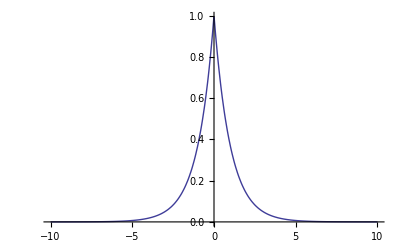

```mathematica
κ=1;Plot[Piecewise[{{ⅇ^(+κ x),x<0},{ⅇ^(-κ x),x≥0}}],{x,-10,10},PlotRange->All]
```

```mathematica
-ℏ^2/(2m)D[ψ,{x,2}]==En ψ
```

```mathematica
ψ=ⅇ^(+κ x);{-ℏ^2/(2m)D[ψ,{x,2}],En ψ}
```

{-(ⅇ^x ℏ^2)/(2 m),ⅇ^x En}

```mathematica
ψ=ⅇ^(-κ x);{-ℏ^2/(2m)D[ψ,{x,2}],En ψ}
```

{-(ⅇ^-x ℏ^2)/(2 m),ⅇ^-x En}

40-60

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;
Subscript[U, 0]=20 ElectronVolt;En=13ElectronVolt;
η=ℏ/(√(2m(Subscript[U, 0]-En)))
Convert[η,Meter]
```

(2.95303×10^-20 Joule Second)/(√(ElectronVolt Kilogram))

7.37755×10^-11 Meter

40-63

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=6.64*10^-27 Kilogram;L=2.0Femto Meter;
Subscript[U, 0]=30*10^6 ElectronVolt;
En=Subscript[U, 0]-1*10^6 ElectronVolt;
κ=(√(2m(Subscript[U, 0]-En)))/ℏ;G=16 En/Subscript[U, 0](1-En/Subscript[U, 0])=;T=G ⅇ^(-2κ L)
Convert[T,1]
```

```mathematica
(1+((Subscript[U, 0] ⅇ^(κ L)/2)^2)/(4En(Subscript[U, 0]-En)))^-1=(1+ⅇ^(2κ L)/((16En(Subscript[U, 0]-En))/Subscript[U, 0]^2))^-1
```

```mathematica
(1+(Subscript[U, 0] Sinh[κ L])^2/(4En(Subscript[U, 0]-En)))^-1->(1+((Subscript[U, 0](√(2m(Subscript[U, 0]-En)))/ℏ )^2(L)^2)/(4En(Subscript[U, 0]-En)))^-1=(1+(Subscript[U, 0](2m) (L)^2)/(4 ℏ^2))
```

40-68

```mathematica
-ℏ^2/(2m)D[ψ,{x,2}]+1/2 k1 x^2 ψ==En ψ
```

```mathematica
ψ=Subscript[A, 1] x Exp[-(m ω)/ℏ*x^2/2];D[ψ,{x,2}](-ℏ^2/(2m))//Simplify
```

-1/2 ⅇ^(-(m x^2 ω)/(2 ℏ)) x ω (m x^2 ω-3 ℏ) A_1

```mathematica
∫_(-∞)^∞ (Subscript[A, 1]^2 x^2 Exp[-(m ω)/ℏ*x^2])ⅆx
```

If[Re[(m ω)/ℏ]>0,(√π)/(2 ((m ω)/ℏ)^(3/2)),Integrate[ⅇ^(-(m x^2 ω)/ℏ) x^2,{x,-∞,∞},Assumptions→Re[(m ω)/ℏ]≤0]] A_1^2

```mathematica
D[ψ,{x,1}]//Simplify
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) (-m x^2 ω+ℏ) A_1)/ℏ

40-69

```mathematica
(h/(L/n))^2 1/(2m)
```

40-70

```mathematica
k=(√(2m En))/ℏ;B Sin[k x];D[B Sin[k x],x]
```

(√2 B √(En m) Cos[(√2 √(En m) x)/ℏ])/ℏ

```mathematica
κ=(√(2m(Subscript[U, 0]-En)))/ℏ;D ⅇ^(-κ x);D[D ⅇ^(-κ x),x]
```

-(√2 D ⅇ^(-(√2 x √(m (-En+U_0)))/ℏ) √(m (-En+U_0)))/ℏ

```mathematica
D[B Sin[k x],x]
D[D ⅇ^(-κ x),x]
```

B k Cos[k x]

-D ⅇ^(-x κ) κ

```mathematica
B Sin[k L]=D ⅇ^(-κ L);B k Cos[L x]=-D ⅇ^(-L κ) κ
B k Cos[L x]=-B Sin[k L] κ
```

40-72

```mathematica
p=h/λ;K=p^2/(2m);En=K+U;
λ=h/p=h/(√(2m K))=h/(√(2m (En-U)))
```

```mathematica
∫_0^L √(2m (En-U))ⅆx==(n h)/2
```

```mathematica
L √(2m En)=(n h)/2;√(2m En)=(n h)/(2L);2m En=((n h)/(2L))^2;En=(n^2 h^2)/(4 L^2*2m)
```

40-73

```mathematica
En=1/2 k1 x^2;x=√((2En)/k1);∫_0^(√((2En)/k1)) √(2m (En-1/2 k1 x^2))ⅆx==(n h)/2;
```

```mathematica
Solve[∫_0^(√((2En)/k1)) √(2m (En-1/2 k1 x^2))ⅆx==(n h)/2,En]
```

```mathematica
∫_0^(√((2En)/k1)) √(2m (En-1/2 k1 x^2))ⅆx=√(2m)∫_0^(√((2En)/k1)) √(En-1/2 k1 x^2)ⅆx
=(√(2m))/(√(k1/2))∫_0^(√((2En)/k1)) √(En-(√(k1/2) x)^2)ⅆ(√(k1/2) x)=(√(2m))/(√(k1/2))1/2(En π/2)
```

```mathematica
Integrate[√(2m (En-1/2 k1 x^2)),{x,0,√((2En)/k1)},
Assumptions->m>0&&k1>0&&En>0]
```

1/2 En √(m/k1) π

```mathematica
Solve[1/2 En √(m/k1) π*2==(n h)/2,En]
```

{{En→(h n)/(2 √(m/k1) π)}}

40-74

```mathematica
∫_0^(En/A) √(2m (En-A x))ⅆx
```

```mathematica
Integrate[√(2m (En-A x)),{x,0,En/A},
Assumptions->m>0&&A>0&&En>0]
```

(2 √2 √(En^3 m))/(3 A)

```mathematica
Solve[(2 √2 √(En^3 m))/(3 A)*2==(n h)/2,En]
```

{{En→((-3)^(2/3) A^(2/3) h^(2/3) n^(2/3))/(4 2^(1/3) m^(1/3))},{En→-((-1/2)^(1/3) 3^(2/3) A^(2/3) h^(2/3) n^(2/3))/(4 m^(1/3))},{En→(3^(2/3) A^(2/3) h^(2/3) n^(2/3))/(4 2^(1/3) m^(1/3))}}

Network

```mathematica
<<PhysicalConstants`;λ=SpeedOfLight/(900 *10^6 Hertz);Convert[λ,Meter]//N
```

0.333103 Meter

```mathematica
<<PhysicalConstants`;λ=SpeedOfLight/(2.4*10^9 Hertz);Convert[λ,Meter]//N
```

0.124914 Meter

```mathematica
<<PhysicalConstants`;λ=SpeedOfLight/(10^11 Hertz);Convert[λ,Meter]//N
```

0.00299792 Meter

Digital Design

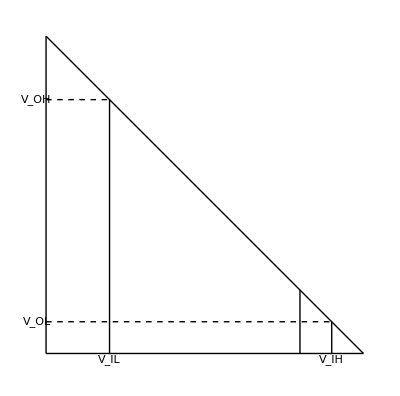

```mathematica
Graphics[{
Line[{{0,5},{5,0}}],
Line[{{1,0},{1,4}}],
Line[{{4,0},{4,1}}],
Line[{{4.5,0},{4.5,0.5}}],
{Dashing[0.01],Line[{{0,4},{1,4}}]},
{Dashing[0.01],Line[{{0,0.5},{4.5,0.5}}]},
Line[{{0,0},{5,0}}],
Line[{{0,0},{0,5}}],
Text[Subscript[V, IL],{1,-0.1}],
Text[Subscript[V, OH],{-0.15,4}],
Text[Subscript[V, IH],{4.5,-0.1}],
Text[Subscript[V, OL],{-0.15,0.5}]
}]
```

```mathematica
Subscript[V, IL]=3;Subscript[V, OH]=4;Subscript[V, IH]=3;Subscript[V, OL]=1.5;
```

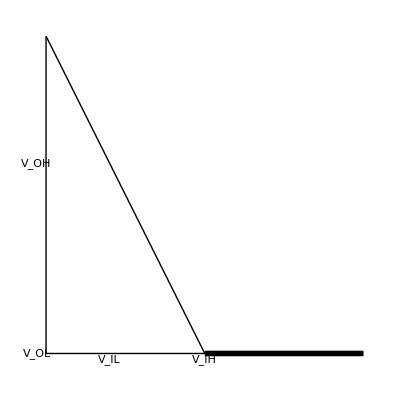

```mathematica
Graphics[{
Line[{{0,0},{5,0}}],
Line[{{0,0},{0,5}}],
Line[{{0,5},{2.5,0}}],
{Thickness[0.01],Line[{{2.5,0},{5,0}}]},
Text[Subscript[V, IL],{1,-0.1}],
Text[Subscript[V, OH],{-0.15,3}],
Text[Subscript[V, IH],{2.5,-0.1}],
Text[Subscript[V, OL],{-0.15,0}]
}]
```

Digital Design1.86

```mathematica
1,0,0->1
```

```mathematica
NOT
YES->NOR
YES
```

Example 41.2

```mathematica
n;1+3+...+(2(n-1)+1)
```

41-MP

```mathematica
Solve[4/3 π(1.47*10^-10)^3==x^3,x]
```

{{x→-1.18481×10^-10-2.05216×10^-10 ⅈ},{x→-1.18481×10^-10+2.05216×10^-10 ⅈ},{x→2.36963×10^-10}}

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;L=2.37*^-10Meter;Subscript[E, 3,2,2];Subscript[E, 3,1,3];En=(19-3)(π^2 ℏ^2)/(2m L^2);f=En/h;Subscript[ϵ, 0]=VacuumPermittivity;q=ElectronCharge;U=q^2/(4π Subscript[ϵ, 0])1/(L/2);
Convert[f,Hertz]
Convert[En,Joule]
Convert[U,Joule]
```

2.59×10^16 Hertz

1.71615×10^-17 Joule

1.9469×10^-18 Joule

```mathematica
2.48*10^15*(22-1)^2
```

1.09368×10^18

Q41.23

```mathematica
<<PhysicalConstants`;h=PlanckConstant;En=-(1/2^2-1)*13.6ElectronVolt;f=En/h;Convert[f,Hertz]
```

2.46635×10^15 Hertz

41-3

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;L=8.00*^-11Meter;c=SpeedOfLight;En=(9-3)(π^2 ℏ^2)/(2m L^2);λ=(c h)/En;
Convert[λ,Meter]
```

3.517×10^-9 Meter

41-5

```mathematica
(Subscript[n, X] π x)/L=0;0<=x<=L;
```

41-7

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);n=4;x=n-1;√(x(x+1))ℏ
Subscript[m, l]=x;Subscript[m, l] ℏ
Subscript[S, z]=1/2 ℏ
```

3.65314×10^-34 Joule Second

3.16371×10^-34 Joule Second

5.27286×10^-35 Joule Second

41-13

```mathematica
18;x=4;θ=ArcCos[x/(√(x(x+1)))];θ/π 180//N
```

26.5651

41-17

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;q=ElectronCharge;Subscript[μ, B]=(q ℏ)/(2 m);U=Subscript[m, l] Subscript[μ, B] B; B=(2.71*10^-5 ElectronVolt)/Subscript[μ, B];Convert[B,Tesla]
```

0.468179 Tesla

41-20

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;q=ElectronCharge;Subscript[μ, B]=(q ℏ)/(2 m);U=Subscript[m, l] Subscript[μ, B] B; B=(2.71*10^-5 ElectronVolt)/Subscript[μ, B];En=-(1/2^2-1)*13.6ElectronVolt;
Convert[En,Joule]
λ=(c h)/En;c=SpeedOfLight;Convert[λ,Meter]
```

1.63422×10^-18 Joule

1.21553×10^-7 Meter

41-21

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);M=ElectronMass;R=1.0*10^-17 Meter;x=(√(3/4)ℏ)/(2/5 M R^2);Convert[x,1/Second]
Convert[x R,Meter/Second]
```

(2.50644×10^30)/Second

(2.50644×10^13 Meter)/Second

41-35

```mathematica
L=2;z=4;
```

```mathematica
<<PhysicalConstants`;En1=-2^2/2^2*13.6ElectronVolt
En2=-2^2/4^2*13.6ElectronVolt
```

-13.6 ElectronVolt

-3.4 ElectronVolt

41-37

```mathematica
<<PhysicalConstants`;Table[(2.48*10^15 Hertz)(Z-1)^2,{Z,{20,27,48}}]
```

{8.9528×10^17 Hertz,1.67648×10^18 Hertz,5.47832×10^18 Hertz}

41-40

```mathematica
∫_0^(L/2) Sin[(π x)/L]^2 ⅆx
∫_0^L Sin[(π x)/L]^2 ⅆx
∫_0^(L/4) Sin[(π x)/L]^2 ⅆx
```

L/4

L/2

(L (-2+π))/(8 π)

```mathematica
(∫_0^(L/4) Sin[(π x)/L]^2 ⅆx)/(∫_0^L Sin[(π x)/L]^2 ⅆx)//N
```

0.0908451

```mathematica
((∫_0^(L/4) Sin[(π x)/L]^2 ⅆx)/(∫_0^L Sin[(π x)/L]^2 ⅆx))^3//N
```

0.000749728

41-45

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);Subscript[E, Subscript[n, x]]=(Subscript[n, x]+1/2)ℏ √((Subscript[k, 1]')/m);
Subscript[E, Subscript[n, z]]=(Subscript[n, z]+1/2)ℏ √((Subscript[k, 2]')/m);1
```

41-47

```mathematica
N;2(1+3+5+...+(2(N-1)+1))=2((1+2(N-1)+1)N)/2=2 N^2
```

41-53

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;Subscript[ϵ, 0]=VacuumPermittivity;q=ElectronCharge;U=-q^2/(4π Subscript[ϵ, 0])1/r;-q^2/(4π Subscript[ϵ, 0])1/r;En=-1/(4π Subscript[ϵ, 0])^2(m q^4)/(2 ℏ^2);-13.60ElectronVolt;r=q^2/(4π Subscript[ϵ, 0](13.60ElectronVolt));a=(Subscript[ϵ, 0] h^2)/(π m q^2);
Convert[r,Meter]
```

1.0588×10^-10 Meter

```mathematica
-q^2/(4π Subscript[ϵ, 0])1/r=-1/(4π Subscript[ϵ, 0])^2(m q^4)/(2 ℏ^2);r=(4π Subscript[ϵ, 0] 2 ℏ^2)/(m q^2)=(Subscript[ϵ, 0] 2 h^2)/(π m q^2)
```

```mathematica
∫_(2a)^∞ (1/(√(π a^3))ⅇ^(-r/a))^2 4π r^2 ⅆr=-4/a^3(-(a r^2)/2-(a^2 r)/2-a^3/4)ⅇ^(-(2r)/a)
```

```mathematica
Clear[a,r];-4/a^3(-(a r^2)/2-(a^2 r)/2-a^3/4)ⅇ^(-(2r)/a)/.r->2a//N
```

0.238103

41-55

```mathematica
∫(1/(√(32 π a^3))(2-r/a)ⅇ^(-r/(2a)))^2 4π r^2 ⅆr
```

(ⅇ^(-r/a) (-8 a^5-8 a^4 r-4 a^3 r^2-a r^4))/(8 a^5)

41-59

```mathematica
D[(1/(√(24  a^5))r ⅇ^(-r/(2a)))^2 r^2,{r,1}]
```

(ⅇ^(-r/a) r^3)/(6 a^5)-(ⅇ^(-r/a) r^4)/(24 a^6)

```mathematica
Solve[(ⅇ^(-r/a) r^3)/(6 a^5)-(ⅇ^(-r/a) r^4)/(24 a^6)==0,r]
```

{{r→0},{r→0},{r→0},{r→4 a}}

41-63

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;q=ElectronCharge;Subscript[μ, B]=(q ℏ)/(2 m);ΔEn;Subscript[μ, B] B;c=SpeedOfLight;λ=575.050*10^-9 Meter;Δλ=0.0462*10^-9 Meter;En=(c h)/λ;
Convert[En Δλ/(λ Subscript[μ, B]),Tesla]
```

2.99254 Tesla

41-67

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;q=ElectronCharge;
```

```mathematica
4;20;
```

41-68

```mathematica
U=-(Z q^2)/(4π Subscript[ϵ, 0])1/r;En=-1/(4π Subscript[ϵ, 0])^2(m Z^2 q^4)/(2 ℏ^2);
```

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);m=ElectronMass;Subscript[ϵ, 0]=VacuumPermittivity;q=ElectronCharge;
```

41-71

```mathematica
<<PhysicalConstants`;h=PlanckConstant;Z=23;En1=-(1/2^2-1)(Z-1)^2*13.6ElectronVolt;En2=-(0-1/1^2)(Z-1)^2*13.6ElectronVolt;
c=SpeedOfLight;λ1=(c h)/En1;λ2=(c h)/En2;
Convert[λ1,Meter]
Convert[λ2,Meter]
```

2.51143×10^-10 Meter

1.88357×10^-10 Meter

41-73

```mathematica
((0+N-1)N)/2+N/2=N^2/2
```

```mathematica
Subscript[E, n]=(n+1/2)ℏ √((Subscript[k, 1]')/m);
```

41-74

```mathematica
m v r==h/(2π);v r==h/(2π m);
(m v^2)/r==1/(4π Subscript[ϵ, 0])(2 q^2)/r^2-1/(4π Subscript[ϵ, 0])q^2/(4 r^2)==7/(16π Subscript[ϵ, 0])q^2/r^2;
```

```mathematica
m v^2 r==7/(16π Subscript[ϵ, 0])q^2;
```

```mathematica
v=(7/(16π Subscript[ϵ, 0])q^2)/(h/(2π))
```

(7 q^2)/(8 h ϵ_0)

```mathematica
r=(h/(2π m))/((7 q^2)/(8 h Subscript[ϵ, 0]))
```

(4 h^2 ϵ_0)/(7 m π q^2)

```mathematica
1/2 m v^2;2*1/2 m((7 q^2)/(8 h Subscript[ϵ, 0]))^2
```

(49 m q^4)/(64 h^2 ϵ_0^2)

```mathematica
-1/(4π Subscript[ϵ, 0])(2 q^2)/r;-2 1/(4π Subscript[ϵ, 0])(2 q^2)/((4 h^2 Subscript[ϵ, 0])/(7 m π q^2))+1/(4π Subscript[ϵ, 0])q^2/(2((4 h^2 Subscript[ϵ, 0])/(7 m π q^2)))
```

-(49 m q^4)/(32 h^2 ϵ_0^2)

```mathematica
<<PhysicalConstants`;h=PlanckConstant;m=ElectronMass;Subscript[ϵ, 0]=VacuumPermittivity;q=ElectronCharge;Convert[-(49 m q^4)/(32 h^2 Subscript[ϵ, 0]^2),ElectronVolt]
Convert[(49 m q^4)/(64 h^2 Subscript[ϵ, 0]^2),ElectronVolt]
```

-166.67 ElectronVolt

83.3348 ElectronVolt

41-75

```mathematica
U=-(Z q^2)/(4π Subscript[ϵ, 0])1/r;En=-1/(4π Subscript[ϵ, 0])^2(m Z^2 q^4)/(2(h/(2π))^2);a=(Subscript[ϵ, 0] h^2)/(π m q^2);
```

```mathematica
(-(Z q^2)/(4π Subscript[ϵ, 0]))/(-1/(4π Subscript[ϵ, 0])^2(m Z^2 q^4)/(2(h/(2π))^2))
```

(2 h^2 ϵ_0)/(m π q^2 Z)

```mathematica
(2a)/Z;
```

```mathematica
Clear[a,r,Z];∫(1/(√(π a^3/Z^3))ⅇ^(-r/a))^2 4π r^2/Z^2 1/Z ⅆr
```

-(ⅇ^(-(2 r)/a) (a^2+2 a r+2 r^2))/a^2

```mathematica
(ⅇ^(-(2 r)/a) (a^2+2 a r+2 r^2))/a^2/.r->2 a//N
```

0.238103

42.3

```mathematica
<<PhysicalConstants`;h=PlanckConstant;c=SpeedOfLight;En=12.4*10^3 ElectronVolt;λ=(h c)/En;Convert[λ,Meter]
```

9.99872×10^-11 Meter

```mathematica
<<PhysicalConstants`;h=PlanckConstant;c=SpeedOfLight;m=ElectronMass;En=150ElectronVolt;λ=h/(√(2m En));Convert[λ,Meter]
```

1.00137×10^-10 Meter

```mathematica
<<PhysicalConstants`;h=PlanckConstant;c=SpeedOfLight;m=ProtonMass;En=0.0818ElectronVolt;λ=h/(√(2m En));Convert[λ,Meter]
```

1.00071×10^-10 Meter

Example 42.6

```mathematica
1/(ⅇ^x+1)+1/(ⅇ^-x+1)=1/(ⅇ^x+1)+1/(1/ⅇ^x+1)=(1+ⅇ^x)/(ⅇ^x+1)=1;
```

42 BRIDGING PROBLEM

```mathematica
<<PhysicalConstants`;h=PlanckConstant;ℏ=h/(2π);
f=1.24*10^14 1/Second;Subscript[m, 1]=1.67*10^-27 Kilogram;Subscript[m, 2]=3.15*10^-26 Kilogram;
Subscript[r, 0]=0.092*10^-9 Meter;l=1;n=1;Ine=(Subscript[m, 1]*Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])Subscript[r, 0]^2;
ΔEl=-l(l+1)ℏ^2/(2 Ine);ΔEn=(n+1/2)ℏ(2π f)-(n-1+1/2)ℏ(2π f);
Convert[ΔEl,Joule]
Convert[ΔEn,Joule]
```

-8.28505×10^-22 Joule

8.21633×10^-20 Joule

### 43

```mathematica
4.002603*3 - 12
```

0.007809

```mathematica
(931.5ElectronVolt)
```

### 43-3

```mathematica
f*h/Subscript[μ, z]/.{f ->Quantity[22.7*10^6, "Hertz"],h->Quantity[1,"PlanckConstant"],Subscript[μ, z]->Quantity[2*2.7928*3.152*10^-8,"Electronvolts"/"Teslas"]}
```

1.28935×10^14 Hz h T/eV

```mathematica
UnitConvert[%,"Teslas"]
```

0.533231 T